```mathematica
Vs = 10;
Es = 15;
gamma = RandomReal[]
```

0.381291

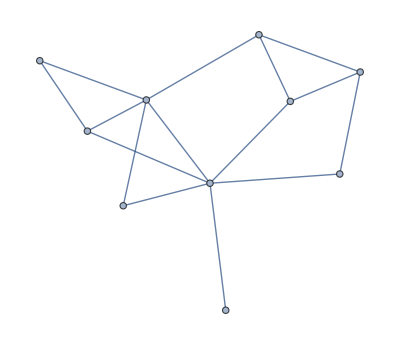

```mathematica
g = RandomGraph[{Vs,Es}]
```

```mathematica
UB = 15
```

15

```mathematica
varsY = Array[y,UB]
```

{y[1],y[2],y[3],y[4],y[5],y[6],y[7],y[8],y[9],y[10],y[11],y[12],y[13],y[14],y[15]}

```mathematica
varsX = Array[x,{UB,Vs}]
```

{{x[1,1],x[1,2],x[1,3],x[1,4],x[1,5],x[1,6],x[1,7],x[1,8],x[1,9],x[1,10]},{x[2,1],x[2,2],x[2,3],x[2,4],x[2,5],x[2,6],x[2,7],x[2,8],x[2,9],x[2,10]},{x[3,1],x[3,2],x[3,3],x[3,4],x[3,5],x[3,6],x[3,7],x[3,8],x[3,9],x[3,10]},{x[4,1],x[4,2],x[4,3],x[4,4],x[4,5],x[4,6],x[4,7],x[4,8],x[4,9],x[4,10]},{x[5,1],x[5,2],x[5,3],x[5,4],x[5,5],x[5,6],x[5,7],x[5,8],x[5,9],x[5,10]},{x[6,1],x[6,2],x[6,3],x[6,4],x[6,5],x[6,6],x[6,7],x[6,8],x[6,9],x[6,10]},{x[7,1],x[7,2],x[7,3],x[7,4],x[7,5],x[7,6],x[7,7],x[7,8],x[7,9],x[7,10]},{x[8,1],x[8,2],x[8,3],x[8,4],x[8,5],x[8,6],x[8,7],x[8,8],x[8,9],x[8,10]},{x[9,1],x[9,2],x[9,3],x[9,4],x[9,5],x[9,6],x[9,7],x[9,8],x[9,9],x[9,10]},{x[10,1],x[10,2],x[10,3],x[10,4],x[10,5],x[10,6],x[10,7],x[10,8],x[10,9],x[10,10]},{x[11,1],x[11,2],x[11,3],x[11,4],x[11,5],x[11,6],x[11,7],x[11,8],x[11,9],x[11,10]},{x[12,1],x[12,2],x[12,3],x[12,4],x[12,5],x[12,6],x[12,7],x[12,8],x[12,9],x[12,10]},{x[13,1],x[13,2],x[13,3],x[13,4],x[13,5],x[13,6],x[13,7],x[13,8],x[13,9],x[13,10]},{x[14,1],x[14,2],x[14,3],x[14,4],x[14,5],x[14,6],x[14,7],x[14,8],x[14,9],x[14,10]},{x[15,1],x[15,2],x[15,3],x[15,4],x[15,5],x[15,6],x[15,7],x[15,8],x[15,9],x[15,10]}}

```mathematica
coupleVs = Tuples[Range[Vs],{2}](*  Всевозможные пары вершин *)
```

{{1,1},{1,2},{1,3},{1,4},{1,5},{1,6},{1,7},{1,8},{1,9},{1,10},{2,1},{2,2},{2,3},{2,4},{2,5},{2,6},{2,7},{2,8},{2,9},{2,10},{3,1},{3,2},{3,3},{3,4},{3,5},{3,6},{3,7},{3,8},{3,9},{3,10},{4,1},{4,2},{4,3},{4,4},{4,5},{4,6},{4,7},{4,8},{4,9},{4,10},{5,1},{5,2},{5,3},{5,4},{5,5},{5,6},{5,7},{5,8},{5,9},{5,10},{6,1},{6,2},{6,3},{6,4},{6,5},{6,6},{6,7},{6,8},{6,9},{6,10},{7,1},{7,2},{7,3},{7,4},{7,5},{7,6},{7,7},{7,8},{7,9},{7,10},{8,1},{8,2},{8,3},{8,4},{8,5},{8,6},{8,7},{8,8},{8,9},{8,10},{9,1},{9,2},{9,3},{9,4},{9,5},{9,6},{9,7},{9,8},{9,9},{9,10},{10,1},{10,2},{10,3},{10,4},{10,5},{10,6},{10,7},{10,8},{10,9},{10,10}}

```mathematica
coupleVs = Table[If[coupleVs[[i,1]]<coupleVs⟦i,2⟧,coupleVs⟦i⟧,Nothing],{i,Length[coupleVs]}] (*Очищаем, так как в бинарной w u<v*)
```

{{1,2},{1,3},{1,4},{1,5},{1,6},{1,7},{1,8},{1,9},{1,10},{2,3},{2,4},{2,5},{2,6},{2,7},{2,8},{2,9},{2,10},{3,4},{3,5},{3,6},{3,7},{3,8},{3,9},{3,10},{4,5},{4,6},{4,7},{4,8},{4,9},{4,10},{5,6},{5,7},{5,8},{5,9},{5,10},{6,7},{6,8},{6,9},{6,10},{7,8},{7,9},{7,10},{8,9},{8,10},{9,10}}

```mathematica
varsW = Table[w[j,coupleVs⟦i,1⟧,coupleVs⟦i,2⟧],{j,UB},{i,Length[coupleVs]}]
```

{{w[1,1,2],w[1,1,3],w[1,1,4],w[1,1,5],w[1,1,6],w[1,1,7],w[1,1,8],w[1,1,9],w[1,1,10],w[1,2,3],w[1,2,4],w[1,2,5],w[1,2,6],w[1,2,7],w[1,2,8],w[1,2,9],w[1,2,10],w[1,3,4],w[1,3,5],w[1,3,6],w[1,3,7],w[1,3,8],w[1,3,9],w[1,3,10],w[1,4,5],w[1,4,6],w[1,4,7],w[1,4,8],w[1,4,9],w[1,4,10],w[1,5,6],w[1,5,7],w[1,5,8],w[1,5,9],w[1,5,10],w[1,6,7],w[1,6,8],w[1,6,9],w[1,6,10],w[1,7,8],w[1,7,9],w[1,7,10],w[1,8,9],w[1,8,10],w[1,9,10]},{w[2,1,2],w[2,1,3],w[2,1,4],w[2,1,5],w[2,1,6],w[2,1,7],w[2,1,8],w[2,1,9],w[2,1,10],w[2,2,3],w[2,2,4],w[2,2,5],w[2,2,6],w[2,2,7],w[2,2,8],w[2,2,9],w[2,2,10],w[2,3,4],w[2,3,5],w[2,3,6],w[2,3,7],w[2,3,8],w[2,3,9],w[2,3,10],w[2,4,5],w[2,4,6],w[2,4,7],w[2,4,8],w[2,4,9],w[2,4,10],w[2,5,6],w[2,5,7],w[2,5,8],w[2,5,9],w[2,5,10],w[2,6,7],w[2,6,8],w[2,6,9],w[2,6,10],w[2,7,8],w[2,7,9],w[2,7,10],w[2,8,9],w[2,8,10],w[2,9,10]},{w[3,1,2],w[3,1,3],w[3,1,4],w[3,1,5],w[3,1,6],w[3,1,7],w[3,1,8],w[3,1,9],w[3,1,10],w[3,2,3],w[3,2,4],w[3,2,5],w[3,2,6],w[3,2,7],w[3,2,8],w[3,2,9],w[3,2,10],w[3,3,4],w[3,3,5],w[3,3,6],w[3,3,7],w[3,3,8],w[3,3,9],w[3,3,10],w[3,4,5],w[3,4,6],w[3,4,7],w[3,4,8],w[3,4,9],w[3,4,10],w[3,5,6],w[3,5,7],w[3,5,8],w[3,5,9],w[3,5,10],w[3,6,7],w[3,6,8],w[3,6,9],w[3,6,10],w[3,7,8],w[3,7,9],w[3,7,10],w[3,8,9],w[3,8,10],w[3,9,10]},{w[4,1,2],w[4,1,3],w[4,1,4],w[4,1,5],w[4,1,6],w[4,1,7],w[4,1,8],w[4,1,9],w[4,1,10],w[4,2,3],w[4,2,4],w[4,2,5],w[4,2,6],w[4,2,7],w[4,2,8],w[4,2,9],w[4,2,10],w[4,3,4],w[4,3,5],w[4,3,6],w[4,3,7],w[4,3,8],w[4,3,9],w[4,3,10],w[4,4,5],w[4,4,6],w[4,4,7],w[4,4,8],w[4,4,9],w[4,4,10],w[4,5,6],w[4,5,7],w[4,5,8],w[4,5,9],w[4,5,10],w[4,6,7],w[4,6,8],w[4,6,9],w[4,6,10],w[4,7,8],w[4,7,9],w[4,7,10],w[4,8,9],w[4,8,10],w[4,9,10]},{w[5,1,2],w[5,1,3],w[5,1,4],w[5,1,5],w[5,1,6],w[5,1,7],w[5,1,8],w[5,1,9],w[5,1,10],w[5,2,3],w[5,2,4],w[5,2,5],w[5,2,6],w[5,2,7],w[5,2,8],w[5,2,9],w[5,2,10],w[5,3,4],w[5,3,5],w[5,3,6],w[5,3,7],w[5,3,8],w[5,3,9],w[5,3,10],w[5,4,5],w[5,4,6],w[5,4,7],w[5,4,8],w[5,4,9],w[5,4,10],w[5,5,6],w[5,5,7],w[5,5,8],w[5,5,9],w[5,5,10],w[5,6,7],w[5,6,8],w[5,6,9],w[5,6,10],w[5,7,8],w[5,7,9],w[5,7,10],w[5,8,9],w[5,8,10],w[5,9,10]},{w[6,1,2],w[6,1,3],w[6,1,4],w[6,1,5],w[6,1,6],w[6,1,7],w[6,1,8],w[6,1,9],w[6,1,10],w[6,2,3],w[6,2,4],w[6,2,5],w[6,2,6],w[6,2,7],w[6,2,8],w[6,2,9],w[6,2,10],w[6,3,4],w[6,3,5],w[6,3,6],w[6,3,7],w[6,3,8],w[6,3,9],w[6,3,10],w[6,4,5],w[6,4,6],w[6,4,7],w[6,4,8],w[6,4,9],w[6,4,10],w[6,5,6],w[6,5,7],w[6,5,8],w[6,5,9],w[6,5,10],w[6,6,7],w[6,6,8],w[6,6,9],w[6,6,10],w[6,7,8],w[6,7,9],w[6,7,10],w[6,8,9],w[6,8,10],w[6,9,10]},{w[7,1,2],w[7,1,3],w[7,1,4],w[7,1,5],w[7,1,6],w[7,1,7],w[7,1,8],w[7,1,9],w[7,1,10],w[7,2,3],w[7,2,4],w[7,2,5],w[7,2,6],w[7,2,7],w[7,2,8],w[7,2,9],w[7,2,10],w[7,3,4],w[7,3,5],w[7,3,6],w[7,3,7],w[7,3,8],w[7,3,9],w[7,3,10],w[7,4,5],w[7,4,6],w[7,4,7],w[7,4,8],w[7,4,9],w[7,4,10],w[7,5,6],w[7,5,7],w[7,5,8],w[7,5,9],w[7,5,10],w[7,6,7],w[7,6,8],w[7,6,9],w[7,6,10],w[7,7,8],w[7,7,9],w[7,7,10],w[7,8,9],w[7,8,10],w[7,9,10]},{w[8,1,2],w[8,1,3],w[8,1,4],w[8,1,5],w[8,1,6],w[8,1,7],w[8,1,8],w[8,1,9],w[8,1,10],w[8,2,3],w[8,2,4],w[8,2,5],w[8,2,6],w[8,2,7],w[8,2,8],w[8,2,9],w[8,2,10],w[8,3,4],w[8,3,5],w[8,3,6],w[8,3,7],w[8,3,8],w[8,3,9],w[8,3,10],w[8,4,5],w[8,4,6],w[8,4,7],w[8,4,8],w[8,4,9],w[8,4,10],w[8,5,6],w[8,5,7],w[8,5,8],w[8,5,9],w[8,5,10],w[8,6,7],w[8,6,8],w[8,6,9],w[8,6,10],w[8,7,8],w[8,7,9],w[8,7,10],w[8,8,9],w[8,8,10],w[8,9,10]},{w[9,1,2],w[9,1,3],w[9,1,4],w[9,1,5],w[9,1,6],w[9,1,7],w[9,1,8],w[9,1,9],w[9,1,10],w[9,2,3],w[9,2,4],w[9,2,5],w[9,2,6],w[9,2,7],w[9,2,8],w[9,2,9],w[9,2,10],w[9,3,4],w[9,3,5],w[9,3,6],w[9,3,7],w[9,3,8],w[9,3,9],w[9,3,10],w[9,4,5],w[9,4,6],w[9,4,7],w[9,4,8],w[9,4,9],w[9,4,10],w[9,5,6],w[9,5,7],w[9,5,8],w[9,5,9],w[9,5,10],w[9,6,7],w[9,6,8],w[9,6,9],w[9,6,10],w[9,7,8],w[9,7,9],w[9,7,10],w[9,8,9],w[9,8,10],w[9,9,10]},{w[10,1,2],w[10,1,3],w[10,1,4],w[10,1,5],w[10,1,6],w[10,1,7],w[10,1,8],w[10,1,9],w[10,1,10],w[10,2,3],w[10,2,4],w[10,2,5],w[10,2,6],w[10,2,7],w[10,2,8],w[10,2,9],w[10,2,10],w[10,3,4],w[10,3,5],w[10,3,6],w[10,3,7],w[10,3,8],w[10,3,9],w[10,3,10],w[10,4,5],w[10,4,6],w[10,4,7],w[10,4,8],w[10,4,9],w[10,4,10],w[10,5,6],w[10,5,7],w[10,5,8],w[10,5,9],w[10,5,10],w[10,6,7],w[10,6,8],w[10,6,9],w[10,6,10],w[10,7,8],w[10,7,9],w[10,7,10],w[10,8,9],w[10,8,10],w[10,9,10]},{w[11,1,2],w[11,1,3],w[11,1,4],w[11,1,5],w[11,1,6],w[11,1,7],w[11,1,8],w[11,1,9],w[11,1,10],w[11,2,3],w[11,2,4],w[11,2,5],w[11,2,6],w[11,2,7],w[11,2,8],w[11,2,9],w[11,2,10],w[11,3,4],w[11,3,5],w[11,3,6],w[11,3,7],w[11,3,8],w[11,3,9],w[11,3,10],w[11,4,5],w[11,4,6],w[11,4,7],w[11,4,8],w[11,4,9],w[11,4,10],w[11,5,6],w[11,5,7],w[11,5,8],w[11,5,9],w[11,5,10],w[11,6,7],w[11,6,8],w[11,6,9],w[11,6,10],w[11,7,8],w[11,7,9],w[11,7,10],w[11,8,9],w[11,8,10],w[11,9,10]},{w[12,1,2],w[12,1,3],w[12,1,4],w[12,1,5],w[12,1,6],w[12,1,7],w[12,1,8],w[12,1,9],w[12,1,10],w[12,2,3],w[12,2,4],w[12,2,5],w[12,2,6],w[12,2,7],w[12,2,8],w[12,2,9],w[12,2,10],w[12,3,4],w[12,3,5],w[12,3,6],w[12,3,7],w[12,3,8],w[12,3,9],w[12,3,10],w[12,4,5],w[12,4,6],w[12,4,7],w[12,4,8],w[12,4,9],w[12,4,10],w[12,5,6],w[12,5,7],w[12,5,8],w[12,5,9],w[12,5,10],w[12,6,7],w[12,6,8],w[12,6,9],w[12,6,10],w[12,7,8],w[12,7,9],w[12,7,10],w[12,8,9],w[12,8,10],w[12,9,10]},{w[13,1,2],w[13,1,3],w[13,1,4],w[13,1,5],w[13,1,6],w[13,1,7],w[13,1,8],w[13,1,9],w[13,1,10],w[13,2,3],w[13,2,4],w[13,2,5],w[13,2,6],w[13,2,7],w[13,2,8],w[13,2,9],w[13,2,10],w[13,3,4],w[13,3,5],w[13,3,6],w[13,3,7],w[13,3,8],w[13,3,9],w[13,3,10],w[13,4,5],w[13,4,6],w[13,4,7],w[13,4,8],w[13,4,9],w[13,4,10],w[13,5,6],w[13,5,7],w[13,5,8],w[13,5,9],w[13,5,10],w[13,6,7],w[13,6,8],w[13,6,9],w[13,6,10],w[13,7,8],w[13,7,9],w[13,7,10],w[13,8,9],w[13,8,10],w[13,9,10]},{w[14,1,2],w[14,1,3],w[14,1,4],w[14,1,5],w[14,1,6],w[14,1,7],w[14,1,8],w[14,1,9],w[14,1,10],w[14,2,3],w[14,2,4],w[14,2,5],w[14,2,6],w[14,2,7],w[14,2,8],w[14,2,9],w[14,2,10],w[14,3,4],w[14,3,5],w[14,3,6],w[14,3,7],w[14,3,8],w[14,3,9],w[14,3,10],w[14,4,5],w[14,4,6],w[14,4,7],w[14,4,8],w[14,4,9],w[14,4,10],w[14,5,6],w[14,5,7],w[14,5,8],w[14,5,9],w[14,5,10],w[14,6,7],w[14,6,8],w[14,6,9],w[14,6,10],w[14,7,8],w[14,7,9],w[14,7,10],w[14,8,9],w[14,8,10],w[14,9,10]},{w[15,1,2],w[15,1,3],w[15,1,4],w[15,1,5],w[15,1,6],w[15,1,7],w[15,1,8],w[15,1,9],w[15,1,10],w[15,2,3],w[15,2,4],w[15,2,5],w[15,2,6],w[15,2,7],w[15,2,8],w[15,2,9],w[15,2,10],w[15,3,4],w[15,3,5],w[15,3,6],w[15,3,7],w[15,3,8],w[15,3,9],w[15,3,10],w[15,4,5],w[15,4,6],w[15,4,7],w[15,4,8],w[15,4,9],w[15,4,10],w[15,5,6],w[15,5,7],w[15,5,8],w[15,5,9],w[15,5,10],w[15,6,7],w[15,6,8],w[15,6,9],w[15,6,10],w[15,7,8],w[15,7,9],w[15,7,10],w[15,8,9],w[15,8,10],w[15,9,10]}}

Целевая функция :

```mathematica
objFun = Total[varsY] (* Символьная целевая функция *)
```

y[1]+y[2]+y[3]+y[4]+y[5]+y[6]+y[7]+y[8]+y[9]+y[10]+y[11]+y[12]+y[13]+y[14]+y[15]

Ограничения :

```mathematica
trX = Transpose[varsX]
```

{{x[1,1],x[2,1],x[3,1],x[4,1],x[5,1],x[6,1],x[7,1],x[8,1],x[9,1],x[10,1],x[11,1],x[12,1],x[13,1],x[14,1],x[15,1]},{x[1,2],x[2,2],x[3,2],x[4,2],x[5,2],x[6,2],x[7,2],x[8,2],x[9,2],x[10,2],x[11,2],x[12,2],x[13,2],x[14,2],x[15,2]},{x[1,3],x[2,3],x[3,3],x[4,3],x[5,3],x[6,3],x[7,3],x[8,3],x[9,3],x[10,3],x[11,3],x[12,3],x[13,3],x[14,3],x[15,3]},{x[1,4],x[2,4],x[3,4],x[4,4],x[5,4],x[6,4],x[7,4],x[8,4],x[9,4],x[10,4],x[11,4],x[12,4],x[13,4],x[14,4],x[15,4]},{x[1,5],x[2,5],x[3,5],x[4,5],x[5,5],x[6,5],x[7,5],x[8,5],x[9,5],x[10,5],x[11,5],x[12,5],x[13,5],x[14,5],x[15,5]},{x[1,6],x[2,6],x[3,6],x[4,6],x[5,6],x[6,6],x[7,6],x[8,6],x[9,6],x[10,6],x[11,6],x[12,6],x[13,6],x[14,6],x[15,6]},{x[1,7],x[2,7],x[3,7],x[4,7],x[5,7],x[6,7],x[7,7],x[8,7],x[9,7],x[10,7],x[11,7],x[12,7],x[13,7],x[14,7],x[15,7]},{x[1,8],x[2,8],x[3,8],x[4,8],x[5,8],x[6,8],x[7,8],x[8,8],x[9,8],x[10,8],x[11,8],x[12,8],x[13,8],x[14,8],x[15,8]},{x[1,9],x[2,9],x[3,9],x[4,9],x[5,9],x[6,9],x[7,9],x[8,9],x[9,9],x[10,9],x[11,9],x[12,9],x[13,9],x[14,9],x[15,9]},{x[1,10],x[2,10],x[3,10],x[4,10],x[5,10],x[6,10],x[7,10],x[8,10],x[9,10],x[10,10],x[11,10],x[12,10],x[13,10],x[14,10],x[15,10]}}

```mathematica
con1 = Table[Total[trX⟦i⟧] == 1,{i,Length[trX]}]
```

{x[1,1]+x[2,1]+x[3,1]+x[4,1]+x[5,1]+x[6,1]+x[7,1]+x[8,1]+x[9,1]+x[10,1]+x[11,1]+x[12,1]+x[13,1]+x[14,1]+x[15,1]==1,x[1,2]+x[2,2]+x[3,2]+x[4,2]+x[5,2]+x[6,2]+x[7,2]+x[8,2]+x[9,2]+x[10,2]+x[11,2]+x[12,2]+x[13,2]+x[14,2]+x[15,2]==1,x[1,3]+x[2,3]+x[3,3]+x[4,3]+x[5,3]+x[6,3]+x[7,3]+x[8,3]+x[9,3]+x[10,3]+x[11,3]+x[12,3]+x[13,3]+x[14,3]+x[15,3]==1,x[1,4]+x[2,4]+x[3,4]+x[4,4]+x[5,4]+x[6,4]+x[7,4]+x[8,4]+x[9,4]+x[10,4]+x[11,4]+x[12,4]+x[13,4]+x[14,4]+x[15,4]==1,x[1,5]+x[2,5]+x[3,5]+x[4,5]+x[5,5]+x[6,5]+x[7,5]+x[8,5]+x[9,5]+x[10,5]+x[11,5]+x[12,5]+x[13,5]+x[14,5]+x[15,5]==1,x[1,6]+x[2,6]+x[3,6]+x[4,6]+x[5,6]+x[6,6]+x[7,6]+x[8,6]+x[9,6]+x[10,6]+x[11,6]+x[12,6]+x[13,6]+x[14,6]+x[15,6]==1,x[1,7]+x[2,7]+x[3,7]+x[4,7]+x[5,7]+x[6,7]+x[7,7]+x[8,7]+x[9,7]+x[10,7]+x[11,7]+x[12,7]+x[13,7]+x[14,7]+x[15,7]==1,x[1,8]+x[2,8]+x[3,8]+x[4,8]+x[5,8]+x[6,8]+x[7,8]+x[8,8]+x[9,8]+x[10,8]+x[11,8]+x[12,8]+x[13,8]+x[14,8]+x[15,8]==1,x[1,9]+x[2,9]+x[3,9]+x[4,9]+x[5,9]+x[6,9]+x[7,9]+x[8,9]+x[9,9]+x[10,9]+x[11,9]+x[12,9]+x[13,9]+x[14,9]+x[15,9]==1,x[1,10]+x[2,10]+x[3,10]+x[4,10]+x[5,10]+x[6,10]+x[7,10]+x[8,10]+x[9,10]+x[10,10]+x[11,10]+x[12,10]+x[13,10]+x[14,10]+x[15,10]==1}

```mathematica
con2 = Flatten[Table[varsX⟦i,j⟧ ≤ varsY⟦i⟧,{i,UB},{j,Length[varsX⟦i⟧]}]]
```

{x[1,1]≤y[1],x[1,2]≤y[1],x[1,3]≤y[1],x[1,4]≤y[1],x[1,5]≤y[1],x[1,6]≤y[1],x[1,7]≤y[1],x[1,8]≤y[1],x[1,9]≤y[1],x[1,10]≤y[1],x[2,1]≤y[2],x[2,2]≤y[2],x[2,3]≤y[2],x[2,4]≤y[2],x[2,5]≤y[2],x[2,6]≤y[2],x[2,7]≤y[2],x[2,8]≤y[2],x[2,9]≤y[2],x[2,10]≤y[2],x[3,1]≤y[3],x[3,2]≤y[3],x[3,3]≤y[3],x[3,4]≤y[3],x[3,5]≤y[3],x[3,6]≤y[3],x[3,7]≤y[3],x[3,8]≤y[3],x[3,9]≤y[3],x[3,10]≤y[3],x[4,1]≤y[4],x[4,2]≤y[4],x[4,3]≤y[4],x[4,4]≤y[4],x[4,5]≤y[4],x[4,6]≤y[4],x[4,7]≤y[4],x[4,8]≤y[4],x[4,9]≤y[4],x[4,10]≤y[4],x[5,1]≤y[5],x[5,2]≤y[5],x[5,3]≤y[5],x[5,4]≤y[5],x[5,5]≤y[5],x[5,6]≤y[5],x[5,7]≤y[5],x[5,8]≤y[5],x[5,9]≤y[5],x[5,10]≤y[5],x[6,1]≤y[6],x[6,2]≤y[6],x[6,3]≤y[6],x[6,4]≤y[6],x[6,5]≤y[6],x[6,6]≤y[6],x[6,7]≤y[6],x[6,8]≤y[6],x[6,9]≤y[6],x[6,10]≤y[6],x[7,1]≤y[7],x[7,2]≤y[7],x[7,3]≤y[7],x[7,4]≤y[7],x[7,5]≤y[7],x[7,6]≤y[7],x[7,7]≤y[7],x[7,8]≤y[7],x[7,9]≤y[7],x[7,10]≤y[7],x[8,1]≤y[8],x[8,2]≤y[8],x[8,3]≤y[8],x[8,4]≤y[8],x[8,5]≤y[8],x[8,6]≤y[8],x[8,7]≤y[8],x[8,8]≤y[8],x[8,9]≤y[8],x[8,10]≤y[8],x[9,1]≤y[9],x[9,2]≤y[9],x[9,3]≤y[9],x[9,4]≤y[9],x[9,5]≤y[9],x[9,6]≤y[9],x[9,7]≤y[9],x[9,8]≤y[9],x[9,9]≤y[9],x[9,10]≤y[9],x[10,1]≤y[10],x[10,2]≤y[10],x[10,3]≤y[10],x[10,4]≤y[10],x[10,5]≤y[10],x[10,6]≤y[10],x[10,7]≤y[10],x[10,8]≤y[10],x[10,9]≤y[10],x[10,10]≤y[10],x[11,1]≤y[11],x[11,2]≤y[11],x[11,3]≤y[11],x[11,4]≤y[11],x[11,5]≤y[11],x[11,6]≤y[11],x[11,7]≤y[11],x[11,8]≤y[11],x[11,9]≤y[11],x[11,10]≤y[11],x[12,1]≤y[12],x[12,2]≤y[12],x[12,3]≤y[12],x[12,4]≤y[12],x[12,5]≤y[12],x[12,6]≤y[12],x[12,7]≤y[12],x[12,8]≤y[12],x[12,9]≤y[12],x[12,10]≤y[12],x[13,1]≤y[13],x[13,2]≤y[13],x[13,3]≤y[13],x[13,4]≤y[13],x[13,5]≤y[13],x[13,6]≤y[13],x[13,7]≤y[13],x[13,8]≤y[13],x[13,9]≤y[13],x[13,10]≤y[13],x[14,1]≤y[14],x[14,2]≤y[14],x[14,3]≤y[14],x[14,4]≤y[14],x[14,5]≤y[14],x[14,6]≤y[14],x[14,7]≤y[14],x[14,8]≤y[14],x[14,9]≤y[14],x[14,10]≤y[14],x[15,1]≤y[15],x[15,2]≤y[15],x[15,3]≤y[15],x[15,4]≤y[15],x[15,5]≤y[15],x[15,6]≤y[15],x[15,7]≤y[15],x[15,8]≤y[15],x[15,9]≤y[15],x[15,10]≤y[15]}

```mathematica
con3 = Flatten[Table[x[i,coupleVs⟦j,1⟧]+x[i,coupleVs⟦j,2⟧]≤w[i,coupleVs⟦j,1⟧,coupleVs⟦j,2⟧]+1,{i,UB},{j,Length[coupleVs]}]]
```

{x[1,1]+x[1,2]≤1+w[1,1,2],x[1,1]+x[1,3]≤1+w[1,1,3],x[1,1]+x[1,4]≤1+w[1,1,4],x[1,1]+x[1,5]≤1+w[1,1,5],x[1,1]+x[1,6]≤1+w[1,1,6],x[1,1]+x[1,7]≤1+w[1,1,7],x[1,1]+x[1,8]≤1+w[1,1,8],x[1,1]+x[1,9]≤1+w[1,1,9],x[1,1]+x[1,10]≤1+w[1,1,10],x[1,2]+x[1,3]≤1+w[1,2,3],x[1,2]+x[1,4]≤1+w[1,2,4],x[1,2]+x[1,5]≤1+w[1,2,5],652,x[15,5]+x[15,10]≤1+w[15,5,10],x[15,6]+x[15,7]≤1+w[15,6,7],x[15,6]+x[15,8]≤1+w[15,6,8],x[15,6]+x[15,9]≤1+w[15,6,9],x[15,6]+x[15,10]≤1+w[15,6,10],x[15,7]+x[15,8]≤1+w[15,7,8],x[15,7]+x[15,9]≤1+w[15,7,9],x[15,7]+x[15,10]≤1+w[15,7,10],x[15,8]+x[15,9]≤1+w[15,8,9],x[15,8]+x[15,10]≤1+w[15,8,10],x[15,9]+x[15,10]≤1+w[15,9,10]}
 |  |  |  |

```mathematica
con4 = Flatten[Table[x[i,coupleVs⟦j,1⟧]≥ w[i,coupleVs⟦j,1⟧,coupleVs⟦j,2⟧],{i,UB},{j,Length[coupleVs]}]]
```

{x[1,1]≥w[1,1,2],x[1,1]≥w[1,1,3],x[1,1]≥w[1,1,4],x[1,1]≥w[1,1,5],x[1,1]≥w[1,1,6],x[1,1]≥w[1,1,7],x[1,1]≥w[1,1,8],x[1,1]≥w[1,1,9],x[1,1]≥w[1,1,10],x[1,2]≥w[1,2,3],x[1,2]≥w[1,2,4],x[1,2]≥w[1,2,5],x[1,2]≥w[1,2,6],x[1,2]≥w[1,2,7],x[1,2]≥w[1,2,8],x[1,2]≥w[1,2,9],x[1,2]≥w[1,2,10],x[1,3]≥w[1,3,4],x[1,3]≥w[1,3,5],x[1,3]≥w[1,3,6],x[1,3]≥w[1,3,7],x[1,3]≥w[1,3,8],x[1,3]≥w[1,3,9],x[1,3]≥w[1,3,10],x[1,4]≥w[1,4,5],x[1,4]≥w[1,4,6],x[1,4]≥w[1,4,7],x[1,4]≥w[1,4,8],x[1,4]≥w[1,4,9],x[1,4]≥w[1,4,10],x[1,5]≥w[1,5,6],x[1,5]≥w[1,5,7],x[1,5]≥w[1,5,8],x[1,5]≥w[1,5,9],x[1,5]≥w[1,5,10],x[1,6]≥w[1,6,7],x[1,6]≥w[1,6,8],x[1,6]≥w[1,6,9],x[1,6]≥w[1,6,10],x[1,7]≥w[1,7,8],x[1,7]≥w[1,7,9],x[1,7]≥w[1,7,10],x[1,8]≥w[1,8,9],x[1,8]≥w[1,8,10],x[1,9]≥w[1,9,10],x[2,1]≥w[2,1,2],x[2,1]≥w[2,1,3],x[2,1]≥w[2,1,4],x[2,1]≥w[2,1,5],x[2,1]≥w[2,1,6],x[2,1]≥w[2,1,7],x[2,1]≥w[2,1,8],x[2,1]≥w[2,1,9],x[2,1]≥w[2,1,10],x[2,2]≥w[2,2,3],x[2,2]≥w[2,2,4],x[2,2]≥w[2,2,5],x[2,2]≥w[2,2,6],x[2,2]≥w[2,2,7],x[2,2]≥w[2,2,8],x[2,2]≥w[2,2,9],x[2,2]≥w[2,2,10],x[2,3]≥w[2,3,4],x[2,3]≥w[2,3,5],x[2,3]≥w[2,3,6],x[2,3]≥w[2,3,7],x[2,3]≥w[2,3,8],x[2,3]≥w[2,3,9],x[2,3]≥w[2,3,10],x[2,4]≥w[2,4,5],x[2,4]≥w[2,4,6],x[2,4]≥w[2,4,7],x[2,4]≥w[2,4,8],x[2,4]≥w[2,4,9],x[2,4]≥w[2,4,10],x[2,5]≥w[2,5,6],x[2,5]≥w[2,5,7],x[2,5]≥w[2,5,8],x[2,5]≥w[2,5,9],x[2,5]≥w[2,5,10],x[2,6]≥w[2,6,7],x[2,6]≥w[2,6,8],x[2,6]≥w[2,6,9],x[2,6]≥w[2,6,10],x[2,7]≥w[2,7,8],x[2,7]≥w[2,7,9],x[2,7]≥w[2,7,10],x[2,8]≥w[2,8,9],x[2,8]≥w[2,8,10],x[2,9]≥w[2,9,10],x[3,1]≥w[3,1,2],x[3,1]≥w[3,1,3],x[3,1]≥w[3,1,4],x[3,1]≥w[3,1,5],x[3,1]≥w[3,1,6],x[3,1]≥w[3,1,7],x[3,1]≥w[3,1,8],x[3,1]≥w[3,1,9],x[3,1]≥w[3,1,10],x[3,2]≥w[3,2,3],x[3,2]≥w[3,2,4],x[3,2]≥w[3,2,5],x[3,2]≥w[3,2,6],x[3,2]≥w[3,2,7],x[3,2]≥w[3,2,8],x[3,2]≥w[3,2,9],x[3,2]≥w[3,2,10],x[3,3]≥w[3,3,4],x[3,3]≥w[3,3,5],x[3,3]≥w[3,3,6],x[3,3]≥w[3,3,7],x[3,3]≥w[3,3,8],x[3,3]≥w[3,3,9],x[3,3]≥w[3,3,10],x[3,4]≥w[3,4,5],x[3,4]≥w[3,4,6],x[3,4]≥w[3,4,7],x[3,4]≥w[3,4,8],x[3,4]≥w[3,4,9],x[3,4]≥w[3,4,10],x[3,5]≥w[3,5,6],x[3,5]≥w[3,5,7],x[3,5]≥w[3,5,8],x[3,5]≥w[3,5,9],x[3,5]≥w[3,5,10],x[3,6]≥w[3,6,7],x[3,6]≥w[3,6,8],x[3,6]≥w[3,6,9],x[3,6]≥w[3,6,10],x[3,7]≥w[3,7,8],x[3,7]≥w[3,7,9],x[3,7]≥w[3,7,10],x[3,8]≥w[3,8,9],x[3,8]≥w[3,8,10],x[3,9]≥w[3,9,10],x[4,1]≥w[4,1,2],x[4,1]≥w[4,1,3],x[4,1]≥w[4,1,4],x[4,1]≥w[4,1,5],x[4,1]≥w[4,1,6],x[4,1]≥w[4,1,7],x[4,1]≥w[4,1,8],x[4,1]≥w[4,1,9],x[4,1]≥w[4,1,10],x[4,2]≥w[4,2,3],x[4,2]≥w[4,2,4],x[4,2]≥w[4,2,5],x[4,2]≥w[4,2,6],x[4,2]≥w[4,2,7],x[4,2]≥w[4,2,8],x[4,2]≥w[4,2,9],x[4,2]≥w[4,2,10],x[4,3]≥w[4,3,4],x[4,3]≥w[4,3,5],x[4,3]≥w[4,3,6],x[4,3]≥w[4,3,7],x[4,3]≥w[4,3,8],x[4,3]≥w[4,3,9],x[4,3]≥w[4,3,10],x[4,4]≥w[4,4,5],x[4,4]≥w[4,4,6],x[4,4]≥w[4,4,7],x[4,4]≥w[4,4,8],x[4,4]≥w[4,4,9],x[4,4]≥w[4,4,10],x[4,5]≥w[4,5,6],x[4,5]≥w[4,5,7],x[4,5]≥w[4,5,8],x[4,5]≥w[4,5,9],x[4,5]≥w[4,5,10],x[4,6]≥w[4,6,7],x[4,6]≥w[4,6,8],x[4,6]≥w[4,6,9],x[4,6]≥w[4,6,10],x[4,7]≥w[4,7,8],x[4,7]≥w[4,7,9],x[4,7]≥w[4,7,10],x[4,8]≥w[4,8,9],x[4,8]≥w[4,8,10],x[4,9]≥w[4,9,10],x[5,1]≥w[5,1,2],x[5,1]≥w[5,1,3],x[5,1]≥w[5,1,4],x[5,1]≥w[5,1,5],x[5,1]≥w[5,1,6],x[5,1]≥w[5,1,7],x[5,1]≥w[5,1,8],x[5,1]≥w[5,1,9],x[5,1]≥w[5,1,10],x[5,2]≥w[5,2,3],x[5,2]≥w[5,2,4],x[5,2]≥w[5,2,5],x[5,2]≥w[5,2,6],x[5,2]≥w[5,2,7],x[5,2]≥w[5,2,8],x[5,2]≥w[5,2,9],x[5,2]≥w[5,2,10],x[5,3]≥w[5,3,4],x[5,3]≥w[5,3,5],x[5,3]≥w[5,3,6],x[5,3]≥w[5,3,7],x[5,3]≥w[5,3,8],x[5,3]≥w[5,3,9],x[5,3]≥w[5,3,10],x[5,4]≥w[5,4,5],x[5,4]≥w[5,4,6],x[5,4]≥w[5,4,7],x[5,4]≥w[5,4,8],x[5,4]≥w[5,4,9],x[5,4]≥w[5,4,10],x[5,5]≥w[5,5,6],x[5,5]≥w[5,5,7],x[5,5]≥w[5,5,8],x[5,5]≥w[5,5,9],x[5,5]≥w[5,5,10],x[5,6]≥w[5,6,7],x[5,6]≥w[5,6,8],x[5,6]≥w[5,6,9],x[5,6]≥w[5,6,10],x[5,7]≥w[5,7,8],x[5,7]≥w[5,7,9],x[5,7]≥w[5,7,10],x[5,8]≥w[5,8,9],x[5,8]≥w[5,8,10],x[5,9]≥w[5,9,10],x[6,1]≥w[6,1,2],x[6,1]≥w[6,1,3],x[6,1]≥w[6,1,4],x[6,1]≥w[6,1,5],x[6,1]≥w[6,1,6],x[6,1]≥w[6,1,7],x[6,1]≥w[6,1,8],x[6,1]≥w[6,1,9],x[6,1]≥w[6,1,10],x[6,2]≥w[6,2,3],x[6,2]≥w[6,2,4],x[6,2]≥w[6,2,5],x[6,2]≥w[6,2,6],x[6,2]≥w[6,2,7],x[6,2]≥w[6,2,8],x[6,2]≥w[6,2,9],x[6,2]≥w[6,2,10],x[6,3]≥w[6,3,4],x[6,3]≥w[6,3,5],x[6,3]≥w[6,3,6],x[6,3]≥w[6,3,7],x[6,3]≥w[6,3,8],x[6,3]≥w[6,3,9],x[6,3]≥w[6,3,10],x[6,4]≥w[6,4,5],x[6,4]≥w[6,4,6],x[6,4]≥w[6,4,7],x[6,4]≥w[6,4,8],x[6,4]≥w[6,4,9],x[6,4]≥w[6,4,10],x[6,5]≥w[6,5,6],x[6,5]≥w[6,5,7],x[6,5]≥w[6,5,8],x[6,5]≥w[6,5,9],x[6,5]≥w[6,5,10],x[6,6]≥w[6,6,7],x[6,6]≥w[6,6,8],x[6,6]≥w[6,6,9],x[6,6]≥w[6,6,10],x[6,7]≥w[6,7,8],x[6,7]≥w[6,7,9],x[6,7]≥w[6,7,10],x[6,8]≥w[6,8,9],x[6,8]≥w[6,8,10],x[6,9]≥w[6,9,10],x[7,1]≥w[7,1,2],x[7,1]≥w[7,1,3],x[7,1]≥w[7,1,4],x[7,1]≥w[7,1,5],x[7,1]≥w[7,1,6],x[7,1]≥w[7,1,7],x[7,1]≥w[7,1,8],x[7,1]≥w[7,1,9],x[7,1]≥w[7,1,10],x[7,2]≥w[7,2,3],x[7,2]≥w[7,2,4],x[7,2]≥w[7,2,5],x[7,2]≥w[7,2,6],x[7,2]≥w[7,2,7],x[7,2]≥w[7,2,8],x[7,2]≥w[7,2,9],x[7,2]≥w[7,2,10],x[7,3]≥w[7,3,4],x[7,3]≥w[7,3,5],x[7,3]≥w[7,3,6],x[7,3]≥w[7,3,7],x[7,3]≥w[7,3,8],x[7,3]≥w[7,3,9],x[7,3]≥w[7,3,10],x[7,4]≥w[7,4,5],x[7,4]≥w[7,4,6],x[7,4]≥w[7,4,7],x[7,4]≥w[7,4,8],x[7,4]≥w[7,4,9],x[7,4]≥w[7,4,10],x[7,5]≥w[7,5,6],x[7,5]≥w[7,5,7],x[7,5]≥w[7,5,8],x[7,5]≥w[7,5,9],x[7,5]≥w[7,5,10],x[7,6]≥w[7,6,7],x[7,6]≥w[7,6,8],x[7,6]≥w[7,6,9],x[7,6]≥w[7,6,10],x[7,7]≥w[7,7,8],x[7,7]≥w[7,7,9],x[7,7]≥w[7,7,10],x[7,8]≥w[7,8,9],x[7,8]≥w[7,8,10],x[7,9]≥w[7,9,10],x[8,1]≥w[8,1,2],x[8,1]≥w[8,1,3],x[8,1]≥w[8,1,4],x[8,1]≥w[8,1,5],x[8,1]≥w[8,1,6],x[8,1]≥w[8,1,7],x[8,1]≥w[8,1,8],x[8,1]≥w[8,1,9],x[8,1]≥w[8,1,10],x[8,2]≥w[8,2,3],x[8,2]≥w[8,2,4],x[8,2]≥w[8,2,5],x[8,2]≥w[8,2,6],x[8,2]≥w[8,2,7],x[8,2]≥w[8,2,8],x[8,2]≥w[8,2,9],x[8,2]≥w[8,2,10],x[8,3]≥w[8,3,4],x[8,3]≥w[8,3,5],x[8,3]≥w[8,3,6],x[8,3]≥w[8,3,7],x[8,3]≥w[8,3,8],x[8,3]≥w[8,3,9],x[8,3]≥w[8,3,10],x[8,4]≥w[8,4,5],x[8,4]≥w[8,4,6],x[8,4]≥w[8,4,7],x[8,4]≥w[8,4,8],x[8,4]≥w[8,4,9],x[8,4]≥w[8,4,10],x[8,5]≥w[8,5,6],x[8,5]≥w[8,5,7],x[8,5]≥w[8,5,8],x[8,5]≥w[8,5,9],x[8,5]≥w[8,5,10],x[8,6]≥w[8,6,7],x[8,6]≥w[8,6,8],x[8,6]≥w[8,6,9],x[8,6]≥w[8,6,10],x[8,7]≥w[8,7,8],x[8,7]≥w[8,7,9],x[8,7]≥w[8,7,10],x[8,8]≥w[8,8,9],x[8,8]≥w[8,8,10],x[8,9]≥w[8,9,10],x[9,1]≥w[9,1,2],x[9,1]≥w[9,1,3],x[9,1]≥w[9,1,4],x[9,1]≥w[9,1,5],x[9,1]≥w[9,1,6],x[9,1]≥w[9,1,7],x[9,1]≥w[9,1,8],x[9,1]≥w[9,1,9],x[9,1]≥w[9,1,10],x[9,2]≥w[9,2,3],x[9,2]≥w[9,2,4],x[9,2]≥w[9,2,5],x[9,2]≥w[9,2,6],x[9,2]≥w[9,2,7],x[9,2]≥w[9,2,8],x[9,2]≥w[9,2,9],x[9,2]≥w[9,2,10],x[9,3]≥w[9,3,4],x[9,3]≥w[9,3,5],x[9,3]≥w[9,3,6],x[9,3]≥w[9,3,7],x[9,3]≥w[9,3,8],x[9,3]≥w[9,3,9],x[9,3]≥w[9,3,10],x[9,4]≥w[9,4,5],x[9,4]≥w[9,4,6],x[9,4]≥w[9,4,7],x[9,4]≥w[9,4,8],x[9,4]≥w[9,4,9],x[9,4]≥w[9,4,10],x[9,5]≥w[9,5,6],x[9,5]≥w[9,5,7],x[9,5]≥w[9,5,8],x[9,5]≥w[9,5,9],x[9,5]≥w[9,5,10],x[9,6]≥w[9,6,7],x[9,6]≥w[9,6,8],x[9,6]≥w[9,6,9],x[9,6]≥w[9,6,10],x[9,7]≥w[9,7,8],x[9,7]≥w[9,7,9],x[9,7]≥w[9,7,10],x[9,8]≥w[9,8,9],x[9,8]≥w[9,8,10],x[9,9]≥w[9,9,10],x[10,1]≥w[10,1,2],x[10,1]≥w[10,1,3],x[10,1]≥w[10,1,4],x[10,1]≥w[10,1,5],x[10,1]≥w[10,1,6],x[10,1]≥w[10,1,7],x[10,1]≥w[10,1,8],x[10,1]≥w[10,1,9],x[10,1]≥w[10,1,10],x[10,2]≥w[10,2,3],x[10,2]≥w[10,2,4],x[10,2]≥w[10,2,5],x[10,2]≥w[10,2,6],x[10,2]≥w[10,2,7],x[10,2]≥w[10,2,8],x[10,2]≥w[10,2,9],x[10,2]≥w[10,2,10],x[10,3]≥w[10,3,4],x[10,3]≥w[10,3,5],x[10,3]≥w[10,3,6],x[10,3]≥w[10,3,7],x[10,3]≥w[10,3,8],x[10,3]≥w[10,3,9],x[10,3]≥w[10,3,10],x[10,4]≥w[10,4,5],x[10,4]≥w[10,4,6],x[10,4]≥w[10,4,7],x[10,4]≥w[10,4,8],x[10,4]≥w[10,4,9],x[10,4]≥w[10,4,10],x[10,5]≥w[10,5,6],x[10,5]≥w[10,5,7],x[10,5]≥w[10,5,8],x[10,5]≥w[10,5,9],x[10,5]≥w[10,5,10],x[10,6]≥w[10,6,7],x[10,6]≥w[10,6,8],x[10,6]≥w[10,6,9],x[10,6]≥w[10,6,10],x[10,7]≥w[10,7,8],x[10,7]≥w[10,7,9],x[10,7]≥w[10,7,10],x[10,8]≥w[10,8,9],x[10,8]≥w[10,8,10],x[10,9]≥w[10,9,10],x[11,1]≥w[11,1,2],x[11,1]≥w[11,1,3],x[11,1]≥w[11,1,4],x[11,1]≥w[11,1,5],x[11,1]≥w[11,1,6],x[11,1]≥w[11,1,7],x[11,1]≥w[11,1,8],x[11,1]≥w[11,1,9],x[11,1]≥w[11,1,10],x[11,2]≥w[11,2,3],x[11,2]≥w[11,2,4],x[11,2]≥w[11,2,5],x[11,2]≥w[11,2,6],x[11,2]≥w[11,2,7],x[11,2]≥w[11,2,8],x[11,2]≥w[11,2,9],x[11,2]≥w[11,2,10],x[11,3]≥w[11,3,4],x[11,3]≥w[11,3,5],x[11,3]≥w[11,3,6],x[11,3]≥w[11,3,7],x[11,3]≥w[11,3,8],x[11,3]≥w[11,3,9],x[11,3]≥w[11,3,10],x[11,4]≥w[11,4,5],x[11,4]≥w[11,4,6],x[11,4]≥w[11,4,7],x[11,4]≥w[11,4,8],x[11,4]≥w[11,4,9],x[11,4]≥w[11,4,10],x[11,5]≥w[11,5,6],x[11,5]≥w[11,5,7],x[11,5]≥w[11,5,8],x[11,5]≥w[11,5,9],x[11,5]≥w[11,5,10],x[11,6]≥w[11,6,7],x[11,6]≥w[11,6,8],x[11,6]≥w[11,6,9],x[11,6]≥w[11,6,10],x[11,7]≥w[11,7,8],x[11,7]≥w[11,7,9],x[11,7]≥w[11,7,10],x[11,8]≥w[11,8,9],x[11,8]≥w[11,8,10],x[11,9]≥w[11,9,10],x[12,1]≥w[12,1,2],x[12,1]≥w[12,1,3],x[12,1]≥w[12,1,4],x[12,1]≥w[12,1,5],x[12,1]≥w[12,1,6],x[12,1]≥w[12,1,7],x[12,1]≥w[12,1,8],x[12,1]≥w[12,1,9],x[12,1]≥w[12,1,10],x[12,2]≥w[12,2,3],x[12,2]≥w[12,2,4],x[12,2]≥w[12,2,5],x[12,2]≥w[12,2,6],x[12,2]≥w[12,2,7],x[12,2]≥w[12,2,8],x[12,2]≥w[12,2,9],x[12,2]≥w[12,2,10],x[12,3]≥w[12,3,4],x[12,3]≥w[12,3,5],x[12,3]≥w[12,3,6],x[12,3]≥w[12,3,7],x[12,3]≥w[12,3,8],x[12,3]≥w[12,3,9],x[12,3]≥w[12,3,10],x[12,4]≥w[12,4,5],x[12,4]≥w[12,4,6],x[12,4]≥w[12,4,7],x[12,4]≥w[12,4,8],x[12,4]≥w[12,4,9],x[12,4]≥w[12,4,10],x[12,5]≥w[12,5,6],x[12,5]≥w[12,5,7],x[12,5]≥w[12,5,8],x[12,5]≥w[12,5,9],x[12,5]≥w[12,5,10],x[12,6]≥w[12,6,7],x[12,6]≥w[12,6,8],x[12,6]≥w[12,6,9],x[12,6]≥w[12,6,10],x[12,7]≥w[12,7,8],x[12,7]≥w[12,7,9],x[12,7]≥w[12,7,10],x[12,8]≥w[12,8,9],x[12,8]≥w[12,8,10],x[12,9]≥w[12,9,10],x[13,1]≥w[13,1,2],x[13,1]≥w[13,1,3],x[13,1]≥w[13,1,4],x[13,1]≥w[13,1,5],x[13,1]≥w[13,1,6],x[13,1]≥w[13,1,7],x[13,1]≥w[13,1,8],x[13,1]≥w[13,1,9],x[13,1]≥w[13,1,10],x[13,2]≥w[13,2,3],x[13,2]≥w[13,2,4],x[13,2]≥w[13,2,5],x[13,2]≥w[13,2,6],x[13,2]≥w[13,2,7],x[13,2]≥w[13,2,8],x[13,2]≥w[13,2,9],x[13,2]≥w[13,2,10],x[13,3]≥w[13,3,4],x[13,3]≥w[13,3,5],x[13,3]≥w[13,3,6],x[13,3]≥w[13,3,7],x[13,3]≥w[13,3,8],x[13,3]≥w[13,3,9],x[13,3]≥w[13,3,10],x[13,4]≥w[13,4,5],x[13,4]≥w[13,4,6],x[13,4]≥w[13,4,7],x[13,4]≥w[13,4,8],x[13,4]≥w[13,4,9],x[13,4]≥w[13,4,10],x[13,5]≥w[13,5,6],x[13,5]≥w[13,5,7],x[13,5]≥w[13,5,8],x[13,5]≥w[13,5,9],x[13,5]≥w[13,5,10],x[13,6]≥w[13,6,7],x[13,6]≥w[13,6,8],x[13,6]≥w[13,6,9],x[13,6]≥w[13,6,10],x[13,7]≥w[13,7,8],x[13,7]≥w[13,7,9],x[13,7]≥w[13,7,10],x[13,8]≥w[13,8,9],x[13,8]≥w[13,8,10],x[13,9]≥w[13,9,10],x[14,1]≥w[14,1,2],x[14,1]≥w[14,1,3],x[14,1]≥w[14,1,4],x[14,1]≥w[14,1,5],x[14,1]≥w[14,1,6],x[14,1]≥w[14,1,7],x[14,1]≥w[14,1,8],x[14,1]≥w[14,1,9],x[14,1]≥w[14,1,10],x[14,2]≥w[14,2,3],x[14,2]≥w[14,2,4],x[14,2]≥w[14,2,5],x[14,2]≥w[14,2,6],x[14,2]≥w[14,2,7],x[14,2]≥w[14,2,8],x[14,2]≥w[14,2,9],x[14,2]≥w[14,2,10],x[14,3]≥w[14,3,4],x[14,3]≥w[14,3,5],x[14,3]≥w[14,3,6],x[14,3]≥w[14,3,7],x[14,3]≥w[14,3,8],x[14,3]≥w[14,3,9],x[14,3]≥w[14,3,10],x[14,4]≥w[14,4,5],x[14,4]≥w[14,4,6],x[14,4]≥w[14,4,7],x[14,4]≥w[14,4,8],x[14,4]≥w[14,4,9],x[14,4]≥w[14,4,10],x[14,5]≥w[14,5,6],x[14,5]≥w[14,5,7],x[14,5]≥w[14,5,8],x[14,5]≥w[14,5,9],x[14,5]≥w[14,5,10],x[14,6]≥w[14,6,7],x[14,6]≥w[14,6,8],x[14,6]≥w[14,6,9],x[14,6]≥w[14,6,10],x[14,7]≥w[14,7,8],x[14,7]≥w[14,7,9],x[14,7]≥w[14,7,10],x[14,8]≥w[14,8,9],x[14,8]≥w[14,8,10],x[14,9]≥w[14,9,10],x[15,1]≥w[15,1,2],x[15,1]≥w[15,1,3],x[15,1]≥w[15,1,4],x[15,1]≥w[15,1,5],x[15,1]≥w[15,1,6],x[15,1]≥w[15,1,7],x[15,1]≥w[15,1,8],x[15,1]≥w[15,1,9],x[15,1]≥w[15,1,10],x[15,2]≥w[15,2,3],x[15,2]≥w[15,2,4],x[15,2]≥w[15,2,5],x[15,2]≥w[15,2,6],x[15,2]≥w[15,2,7],x[15,2]≥w[15,2,8],x[15,2]≥w[15,2,9],x[15,2]≥w[15,2,10],x[15,3]≥w[15,3,4],x[15,3]≥w[15,3,5],x[15,3]≥w[15,3,6],x[15,3]≥w[15,3,7],x[15,3]≥w[15,3,8],x[15,3]≥w[15,3,9],x[15,3]≥w[15,3,10],x[15,4]≥w[15,4,5],x[15,4]≥w[15,4,6],x[15,4]≥w[15,4,7],x[15,4]≥w[15,4,8],x[15,4]≥w[15,4,9],x[15,4]≥w[15,4,10],x[15,5]≥w[15,5,6],x[15,5]≥w[15,5,7],x[15,5]≥w[15,5,8],x[15,5]≥w[15,5,9],x[15,5]≥w[15,5,10],x[15,6]≥w[15,6,7],x[15,6]≥w[15,6,8],x[15,6]≥w[15,6,9],x[15,6]≥w[15,6,10],x[15,7]≥w[15,7,8],x[15,7]≥w[15,7,9],x[15,7]≥w[15,7,10],x[15,8]≥w[15,8,9],x[15,8]≥w[15,8,10],x[15,9]≥w[15,9,10]}

```mathematica
con5 = Flatten[Table[x[i,coupleVs⟦j,2⟧]≥ w[i,coupleVs⟦j,1⟧,coupleVs⟦j,2⟧],{i,UB},{j,Length[coupleVs]}]]
```

{x[1,2]≥w[1,1,2],x[1,3]≥w[1,1,3],x[1,4]≥w[1,1,4],x[1,5]≥w[1,1,5],x[1,6]≥w[1,1,6],x[1,7]≥w[1,1,7],x[1,8]≥w[1,1,8],x[1,9]≥w[1,1,9],x[1,10]≥w[1,1,10],x[1,3]≥w[1,2,3],x[1,4]≥w[1,2,4],x[1,5]≥w[1,2,5],x[1,6]≥w[1,2,6],x[1,7]≥w[1,2,7],x[1,8]≥w[1,2,8],x[1,9]≥w[1,2,9],x[1,10]≥w[1,2,10],x[1,4]≥w[1,3,4],x[1,5]≥w[1,3,5],x[1,6]≥w[1,3,6],x[1,7]≥w[1,3,7],x[1,8]≥w[1,3,8],x[1,9]≥w[1,3,9],x[1,10]≥w[1,3,10],x[1,5]≥w[1,4,5],x[1,6]≥w[1,4,6],x[1,7]≥w[1,4,7],x[1,8]≥w[1,4,8],x[1,9]≥w[1,4,9],x[1,10]≥w[1,4,10],x[1,6]≥w[1,5,6],x[1,7]≥w[1,5,7],x[1,8]≥w[1,5,8],x[1,9]≥w[1,5,9],x[1,10]≥w[1,5,10],x[1,7]≥w[1,6,7],x[1,8]≥w[1,6,8],x[1,9]≥w[1,6,9],x[1,10]≥w[1,6,10],x[1,8]≥w[1,7,8],x[1,9]≥w[1,7,9],x[1,10]≥w[1,7,10],x[1,9]≥w[1,8,9],x[1,10]≥w[1,8,10],x[1,10]≥w[1,9,10],x[2,2]≥w[2,1,2],x[2,3]≥w[2,1,3],x[2,4]≥w[2,1,4],x[2,5]≥w[2,1,5],x[2,6]≥w[2,1,6],x[2,7]≥w[2,1,7],x[2,8]≥w[2,1,8],x[2,9]≥w[2,1,9],x[2,10]≥w[2,1,10],x[2,3]≥w[2,2,3],x[2,4]≥w[2,2,4],x[2,5]≥w[2,2,5],x[2,6]≥w[2,2,6],x[2,7]≥w[2,2,7],x[2,8]≥w[2,2,8],x[2,9]≥w[2,2,9],x[2,10]≥w[2,2,10],x[2,4]≥w[2,3,4],x[2,5]≥w[2,3,5],x[2,6]≥w[2,3,6],x[2,7]≥w[2,3,7],x[2,8]≥w[2,3,8],x[2,9]≥w[2,3,9],x[2,10]≥w[2,3,10],x[2,5]≥w[2,4,5],x[2,6]≥w[2,4,6],x[2,7]≥w[2,4,7],x[2,8]≥w[2,4,8],x[2,9]≥w[2,4,9],x[2,10]≥w[2,4,10],x[2,6]≥w[2,5,6],x[2,7]≥w[2,5,7],x[2,8]≥w[2,5,8],x[2,9]≥w[2,5,9],x[2,10]≥w[2,5,10],x[2,7]≥w[2,6,7],x[2,8]≥w[2,6,8],x[2,9]≥w[2,6,9],x[2,10]≥w[2,6,10],x[2,8]≥w[2,7,8],x[2,9]≥w[2,7,9],x[2,10]≥w[2,7,10],x[2,9]≥w[2,8,9],x[2,10]≥w[2,8,10],x[2,10]≥w[2,9,10],x[3,2]≥w[3,1,2],x[3,3]≥w[3,1,3],x[3,4]≥w[3,1,4],x[3,5]≥w[3,1,5],x[3,6]≥w[3,1,6],x[3,7]≥w[3,1,7],x[3,8]≥w[3,1,8],x[3,9]≥w[3,1,9],x[3,10]≥w[3,1,10],x[3,3]≥w[3,2,3],x[3,4]≥w[3,2,4],x[3,5]≥w[3,2,5],x[3,6]≥w[3,2,6],x[3,7]≥w[3,2,7],x[3,8]≥w[3,2,8],x[3,9]≥w[3,2,9],x[3,10]≥w[3,2,10],x[3,4]≥w[3,3,4],x[3,5]≥w[3,3,5],x[3,6]≥w[3,3,6],x[3,7]≥w[3,3,7],x[3,8]≥w[3,3,8],x[3,9]≥w[3,3,9],x[3,10]≥w[3,3,10],x[3,5]≥w[3,4,5],x[3,6]≥w[3,4,6],x[3,7]≥w[3,4,7],x[3,8]≥w[3,4,8],x[3,9]≥w[3,4,9],x[3,10]≥w[3,4,10],x[3,6]≥w[3,5,6],x[3,7]≥w[3,5,7],x[3,8]≥w[3,5,8],x[3,9]≥w[3,5,9],x[3,10]≥w[3,5,10],x[3,7]≥w[3,6,7],x[3,8]≥w[3,6,8],x[3,9]≥w[3,6,9],x[3,10]≥w[3,6,10],x[3,8]≥w[3,7,8],x[3,9]≥w[3,7,9],x[3,10]≥w[3,7,10],x[3,9]≥w[3,8,9],x[3,10]≥w[3,8,10],x[3,10]≥w[3,9,10],x[4,2]≥w[4,1,2],x[4,3]≥w[4,1,3],x[4,4]≥w[4,1,4],x[4,5]≥w[4,1,5],x[4,6]≥w[4,1,6],x[4,7]≥w[4,1,7],x[4,8]≥w[4,1,8],x[4,9]≥w[4,1,9],x[4,10]≥w[4,1,10],x[4,3]≥w[4,2,3],x[4,4]≥w[4,2,4],x[4,5]≥w[4,2,5],x[4,6]≥w[4,2,6],x[4,7]≥w[4,2,7],x[4,8]≥w[4,2,8],x[4,9]≥w[4,2,9],x[4,10]≥w[4,2,10],x[4,4]≥w[4,3,4],x[4,5]≥w[4,3,5],x[4,6]≥w[4,3,6],x[4,7]≥w[4,3,7],x[4,8]≥w[4,3,8],x[4,9]≥w[4,3,9],x[4,10]≥w[4,3,10],x[4,5]≥w[4,4,5],x[4,6]≥w[4,4,6],x[4,7]≥w[4,4,7],x[4,8]≥w[4,4,8],x[4,9]≥w[4,4,9],x[4,10]≥w[4,4,10],x[4,6]≥w[4,5,6],x[4,7]≥w[4,5,7],x[4,8]≥w[4,5,8],x[4,9]≥w[4,5,9],x[4,10]≥w[4,5,10],x[4,7]≥w[4,6,7],x[4,8]≥w[4,6,8],x[4,9]≥w[4,6,9],x[4,10]≥w[4,6,10],x[4,8]≥w[4,7,8],x[4,9]≥w[4,7,9],x[4,10]≥w[4,7,10],x[4,9]≥w[4,8,9],x[4,10]≥w[4,8,10],x[4,10]≥w[4,9,10],x[5,2]≥w[5,1,2],x[5,3]≥w[5,1,3],x[5,4]≥w[5,1,4],x[5,5]≥w[5,1,5],x[5,6]≥w[5,1,6],x[5,7]≥w[5,1,7],x[5,8]≥w[5,1,8],x[5,9]≥w[5,1,9],x[5,10]≥w[5,1,10],x[5,3]≥w[5,2,3],x[5,4]≥w[5,2,4],x[5,5]≥w[5,2,5],x[5,6]≥w[5,2,6],x[5,7]≥w[5,2,7],x[5,8]≥w[5,2,8],x[5,9]≥w[5,2,9],x[5,10]≥w[5,2,10],x[5,4]≥w[5,3,4],x[5,5]≥w[5,3,5],x[5,6]≥w[5,3,6],x[5,7]≥w[5,3,7],x[5,8]≥w[5,3,8],x[5,9]≥w[5,3,9],x[5,10]≥w[5,3,10],x[5,5]≥w[5,4,5],x[5,6]≥w[5,4,6],x[5,7]≥w[5,4,7],x[5,8]≥w[5,4,8],x[5,9]≥w[5,4,9],x[5,10]≥w[5,4,10],x[5,6]≥w[5,5,6],x[5,7]≥w[5,5,7],x[5,8]≥w[5,5,8],x[5,9]≥w[5,5,9],x[5,10]≥w[5,5,10],x[5,7]≥w[5,6,7],x[5,8]≥w[5,6,8],x[5,9]≥w[5,6,9],x[5,10]≥w[5,6,10],x[5,8]≥w[5,7,8],x[5,9]≥w[5,7,9],x[5,10]≥w[5,7,10],x[5,9]≥w[5,8,9],x[5,10]≥w[5,8,10],x[5,10]≥w[5,9,10],x[6,2]≥w[6,1,2],x[6,3]≥w[6,1,3],x[6,4]≥w[6,1,4],x[6,5]≥w[6,1,5],x[6,6]≥w[6,1,6],x[6,7]≥w[6,1,7],x[6,8]≥w[6,1,8],x[6,9]≥w[6,1,9],x[6,10]≥w[6,1,10],x[6,3]≥w[6,2,3],x[6,4]≥w[6,2,4],x[6,5]≥w[6,2,5],x[6,6]≥w[6,2,6],x[6,7]≥w[6,2,7],x[6,8]≥w[6,2,8],x[6,9]≥w[6,2,9],x[6,10]≥w[6,2,10],x[6,4]≥w[6,3,4],x[6,5]≥w[6,3,5],x[6,6]≥w[6,3,6],x[6,7]≥w[6,3,7],x[6,8]≥w[6,3,8],x[6,9]≥w[6,3,9],x[6,10]≥w[6,3,10],x[6,5]≥w[6,4,5],x[6,6]≥w[6,4,6],x[6,7]≥w[6,4,7],x[6,8]≥w[6,4,8],x[6,9]≥w[6,4,9],x[6,10]≥w[6,4,10],x[6,6]≥w[6,5,6],x[6,7]≥w[6,5,7],x[6,8]≥w[6,5,8],x[6,9]≥w[6,5,9],x[6,10]≥w[6,5,10],x[6,7]≥w[6,6,7],x[6,8]≥w[6,6,8],x[6,9]≥w[6,6,9],x[6,10]≥w[6,6,10],x[6,8]≥w[6,7,8],x[6,9]≥w[6,7,9],x[6,10]≥w[6,7,10],x[6,9]≥w[6,8,9],x[6,10]≥w[6,8,10],x[6,10]≥w[6,9,10],x[7,2]≥w[7,1,2],x[7,3]≥w[7,1,3],x[7,4]≥w[7,1,4],x[7,5]≥w[7,1,5],x[7,6]≥w[7,1,6],x[7,7]≥w[7,1,7],x[7,8]≥w[7,1,8],x[7,9]≥w[7,1,9],x[7,10]≥w[7,1,10],x[7,3]≥w[7,2,3],x[7,4]≥w[7,2,4],x[7,5]≥w[7,2,5],x[7,6]≥w[7,2,6],x[7,7]≥w[7,2,7],x[7,8]≥w[7,2,8],x[7,9]≥w[7,2,9],x[7,10]≥w[7,2,10],x[7,4]≥w[7,3,4],x[7,5]≥w[7,3,5],x[7,6]≥w[7,3,6],x[7,7]≥w[7,3,7],x[7,8]≥w[7,3,8],x[7,9]≥w[7,3,9],x[7,10]≥w[7,3,10],x[7,5]≥w[7,4,5],x[7,6]≥w[7,4,6],x[7,7]≥w[7,4,7],x[7,8]≥w[7,4,8],x[7,9]≥w[7,4,9],x[7,10]≥w[7,4,10],x[7,6]≥w[7,5,6],x[7,7]≥w[7,5,7],x[7,8]≥w[7,5,8],x[7,9]≥w[7,5,9],x[7,10]≥w[7,5,10],x[7,7]≥w[7,6,7],x[7,8]≥w[7,6,8],x[7,9]≥w[7,6,9],x[7,10]≥w[7,6,10],x[7,8]≥w[7,7,8],x[7,9]≥w[7,7,9],x[7,10]≥w[7,7,10],x[7,9]≥w[7,8,9],x[7,10]≥w[7,8,10],x[7,10]≥w[7,9,10],x[8,2]≥w[8,1,2],x[8,3]≥w[8,1,3],x[8,4]≥w[8,1,4],x[8,5]≥w[8,1,5],x[8,6]≥w[8,1,6],x[8,7]≥w[8,1,7],x[8,8]≥w[8,1,8],x[8,9]≥w[8,1,9],x[8,10]≥w[8,1,10],x[8,3]≥w[8,2,3],x[8,4]≥w[8,2,4],x[8,5]≥w[8,2,5],x[8,6]≥w[8,2,6],x[8,7]≥w[8,2,7],x[8,8]≥w[8,2,8],x[8,9]≥w[8,2,9],x[8,10]≥w[8,2,10],x[8,4]≥w[8,3,4],x[8,5]≥w[8,3,5],x[8,6]≥w[8,3,6],x[8,7]≥w[8,3,7],x[8,8]≥w[8,3,8],x[8,9]≥w[8,3,9],x[8,10]≥w[8,3,10],x[8,5]≥w[8,4,5],x[8,6]≥w[8,4,6],x[8,7]≥w[8,4,7],x[8,8]≥w[8,4,8],x[8,9]≥w[8,4,9],x[8,10]≥w[8,4,10],x[8,6]≥w[8,5,6],x[8,7]≥w[8,5,7],x[8,8]≥w[8,5,8],x[8,9]≥w[8,5,9],x[8,10]≥w[8,5,10],x[8,7]≥w[8,6,7],x[8,8]≥w[8,6,8],x[8,9]≥w[8,6,9],x[8,10]≥w[8,6,10],x[8,8]≥w[8,7,8],x[8,9]≥w[8,7,9],x[8,10]≥w[8,7,10],x[8,9]≥w[8,8,9],x[8,10]≥w[8,8,10],x[8,10]≥w[8,9,10],x[9,2]≥w[9,1,2],x[9,3]≥w[9,1,3],x[9,4]≥w[9,1,4],x[9,5]≥w[9,1,5],x[9,6]≥w[9,1,6],x[9,7]≥w[9,1,7],x[9,8]≥w[9,1,8],x[9,9]≥w[9,1,9],x[9,10]≥w[9,1,10],x[9,3]≥w[9,2,3],x[9,4]≥w[9,2,4],x[9,5]≥w[9,2,5],x[9,6]≥w[9,2,6],x[9,7]≥w[9,2,7],x[9,8]≥w[9,2,8],x[9,9]≥w[9,2,9],x[9,10]≥w[9,2,10],x[9,4]≥w[9,3,4],x[9,5]≥w[9,3,5],x[9,6]≥w[9,3,6],x[9,7]≥w[9,3,7],x[9,8]≥w[9,3,8],x[9,9]≥w[9,3,9],x[9,10]≥w[9,3,10],x[9,5]≥w[9,4,5],x[9,6]≥w[9,4,6],x[9,7]≥w[9,4,7],x[9,8]≥w[9,4,8],x[9,9]≥w[9,4,9],x[9,10]≥w[9,4,10],x[9,6]≥w[9,5,6],x[9,7]≥w[9,5,7],x[9,8]≥w[9,5,8],x[9,9]≥w[9,5,9],x[9,10]≥w[9,5,10],x[9,7]≥w[9,6,7],x[9,8]≥w[9,6,8],x[9,9]≥w[9,6,9],x[9,10]≥w[9,6,10],x[9,8]≥w[9,7,8],x[9,9]≥w[9,7,9],x[9,10]≥w[9,7,10],x[9,9]≥w[9,8,9],x[9,10]≥w[9,8,10],x[9,10]≥w[9,9,10],x[10,2]≥w[10,1,2],x[10,3]≥w[10,1,3],x[10,4]≥w[10,1,4],x[10,5]≥w[10,1,5],x[10,6]≥w[10,1,6],x[10,7]≥w[10,1,7],x[10,8]≥w[10,1,8],x[10,9]≥w[10,1,9],x[10,10]≥w[10,1,10],x[10,3]≥w[10,2,3],x[10,4]≥w[10,2,4],x[10,5]≥w[10,2,5],x[10,6]≥w[10,2,6],x[10,7]≥w[10,2,7],x[10,8]≥w[10,2,8],x[10,9]≥w[10,2,9],x[10,10]≥w[10,2,10],x[10,4]≥w[10,3,4],x[10,5]≥w[10,3,5],x[10,6]≥w[10,3,6],x[10,7]≥w[10,3,7],x[10,8]≥w[10,3,8],x[10,9]≥w[10,3,9],x[10,10]≥w[10,3,10],x[10,5]≥w[10,4,5],x[10,6]≥w[10,4,6],x[10,7]≥w[10,4,7],x[10,8]≥w[10,4,8],x[10,9]≥w[10,4,9],x[10,10]≥w[10,4,10],x[10,6]≥w[10,5,6],x[10,7]≥w[10,5,7],x[10,8]≥w[10,5,8],x[10,9]≥w[10,5,9],x[10,10]≥w[10,5,10],x[10,7]≥w[10,6,7],x[10,8]≥w[10,6,8],x[10,9]≥w[10,6,9],x[10,10]≥w[10,6,10],x[10,8]≥w[10,7,8],x[10,9]≥w[10,7,9],x[10,10]≥w[10,7,10],x[10,9]≥w[10,8,9],x[10,10]≥w[10,8,10],x[10,10]≥w[10,9,10],x[11,2]≥w[11,1,2],x[11,3]≥w[11,1,3],x[11,4]≥w[11,1,4],x[11,5]≥w[11,1,5],x[11,6]≥w[11,1,6],x[11,7]≥w[11,1,7],x[11,8]≥w[11,1,8],x[11,9]≥w[11,1,9],x[11,10]≥w[11,1,10],x[11,3]≥w[11,2,3],x[11,4]≥w[11,2,4],x[11,5]≥w[11,2,5],x[11,6]≥w[11,2,6],x[11,7]≥w[11,2,7],x[11,8]≥w[11,2,8],x[11,9]≥w[11,2,9],x[11,10]≥w[11,2,10],x[11,4]≥w[11,3,4],x[11,5]≥w[11,3,5],x[11,6]≥w[11,3,6],x[11,7]≥w[11,3,7],x[11,8]≥w[11,3,8],x[11,9]≥w[11,3,9],x[11,10]≥w[11,3,10],x[11,5]≥w[11,4,5],x[11,6]≥w[11,4,6],x[11,7]≥w[11,4,7],x[11,8]≥w[11,4,8],x[11,9]≥w[11,4,9],x[11,10]≥w[11,4,10],x[11,6]≥w[11,5,6],x[11,7]≥w[11,5,7],x[11,8]≥w[11,5,8],x[11,9]≥w[11,5,9],x[11,10]≥w[11,5,10],x[11,7]≥w[11,6,7],x[11,8]≥w[11,6,8],x[11,9]≥w[11,6,9],x[11,10]≥w[11,6,10],x[11,8]≥w[11,7,8],x[11,9]≥w[11,7,9],x[11,10]≥w[11,7,10],x[11,9]≥w[11,8,9],x[11,10]≥w[11,8,10],x[11,10]≥w[11,9,10],x[12,2]≥w[12,1,2],x[12,3]≥w[12,1,3],x[12,4]≥w[12,1,4],x[12,5]≥w[12,1,5],x[12,6]≥w[12,1,6],x[12,7]≥w[12,1,7],x[12,8]≥w[12,1,8],x[12,9]≥w[12,1,9],x[12,10]≥w[12,1,10],x[12,3]≥w[12,2,3],x[12,4]≥w[12,2,4],x[12,5]≥w[12,2,5],x[12,6]≥w[12,2,6],x[12,7]≥w[12,2,7],x[12,8]≥w[12,2,8],x[12,9]≥w[12,2,9],x[12,10]≥w[12,2,10],x[12,4]≥w[12,3,4],x[12,5]≥w[12,3,5],x[12,6]≥w[12,3,6],x[12,7]≥w[12,3,7],x[12,8]≥w[12,3,8],x[12,9]≥w[12,3,9],x[12,10]≥w[12,3,10],x[12,5]≥w[12,4,5],x[12,6]≥w[12,4,6],x[12,7]≥w[12,4,7],x[12,8]≥w[12,4,8],x[12,9]≥w[12,4,9],x[12,10]≥w[12,4,10],x[12,6]≥w[12,5,6],x[12,7]≥w[12,5,7],x[12,8]≥w[12,5,8],x[12,9]≥w[12,5,9],x[12,10]≥w[12,5,10],x[12,7]≥w[12,6,7],x[12,8]≥w[12,6,8],x[12,9]≥w[12,6,9],x[12,10]≥w[12,6,10],x[12,8]≥w[12,7,8],x[12,9]≥w[12,7,9],x[12,10]≥w[12,7,10],x[12,9]≥w[12,8,9],x[12,10]≥w[12,8,10],x[12,10]≥w[12,9,10],x[13,2]≥w[13,1,2],x[13,3]≥w[13,1,3],x[13,4]≥w[13,1,4],x[13,5]≥w[13,1,5],x[13,6]≥w[13,1,6],x[13,7]≥w[13,1,7],x[13,8]≥w[13,1,8],x[13,9]≥w[13,1,9],x[13,10]≥w[13,1,10],x[13,3]≥w[13,2,3],x[13,4]≥w[13,2,4],x[13,5]≥w[13,2,5],x[13,6]≥w[13,2,6],x[13,7]≥w[13,2,7],x[13,8]≥w[13,2,8],x[13,9]≥w[13,2,9],x[13,10]≥w[13,2,10],x[13,4]≥w[13,3,4],x[13,5]≥w[13,3,5],x[13,6]≥w[13,3,6],x[13,7]≥w[13,3,7],x[13,8]≥w[13,3,8],x[13,9]≥w[13,3,9],x[13,10]≥w[13,3,10],x[13,5]≥w[13,4,5],x[13,6]≥w[13,4,6],x[13,7]≥w[13,4,7],x[13,8]≥w[13,4,8],x[13,9]≥w[13,4,9],x[13,10]≥w[13,4,10],x[13,6]≥w[13,5,6],x[13,7]≥w[13,5,7],x[13,8]≥w[13,5,8],x[13,9]≥w[13,5,9],x[13,10]≥w[13,5,10],x[13,7]≥w[13,6,7],x[13,8]≥w[13,6,8],x[13,9]≥w[13,6,9],x[13,10]≥w[13,6,10],x[13,8]≥w[13,7,8],x[13,9]≥w[13,7,9],x[13,10]≥w[13,7,10],x[13,9]≥w[13,8,9],x[13,10]≥w[13,8,10],x[13,10]≥w[13,9,10],x[14,2]≥w[14,1,2],x[14,3]≥w[14,1,3],x[14,4]≥w[14,1,4],x[14,5]≥w[14,1,5],x[14,6]≥w[14,1,6],x[14,7]≥w[14,1,7],x[14,8]≥w[14,1,8],x[14,9]≥w[14,1,9],x[14,10]≥w[14,1,10],x[14,3]≥w[14,2,3],x[14,4]≥w[14,2,4],x[14,5]≥w[14,2,5],x[14,6]≥w[14,2,6],x[14,7]≥w[14,2,7],x[14,8]≥w[14,2,8],x[14,9]≥w[14,2,9],x[14,10]≥w[14,2,10],x[14,4]≥w[14,3,4],x[14,5]≥w[14,3,5],x[14,6]≥w[14,3,6],x[14,7]≥w[14,3,7],x[14,8]≥w[14,3,8],x[14,9]≥w[14,3,9],x[14,10]≥w[14,3,10],x[14,5]≥w[14,4,5],x[14,6]≥w[14,4,6],x[14,7]≥w[14,4,7],x[14,8]≥w[14,4,8],x[14,9]≥w[14,4,9],x[14,10]≥w[14,4,10],x[14,6]≥w[14,5,6],x[14,7]≥w[14,5,7],x[14,8]≥w[14,5,8],x[14,9]≥w[14,5,9],x[14,10]≥w[14,5,10],x[14,7]≥w[14,6,7],x[14,8]≥w[14,6,8],x[14,9]≥w[14,6,9],x[14,10]≥w[14,6,10],x[14,8]≥w[14,7,8],x[14,9]≥w[14,7,9],x[14,10]≥w[14,7,10],x[14,9]≥w[14,8,9],x[14,10]≥w[14,8,10],x[14,10]≥w[14,9,10],x[15,2]≥w[15,1,2],x[15,3]≥w[15,1,3],x[15,4]≥w[15,1,4],x[15,5]≥w[15,1,5],x[15,6]≥w[15,1,6],x[15,7]≥w[15,1,7],x[15,8]≥w[15,1,8],x[15,9]≥w[15,1,9],x[15,10]≥w[15,1,10],x[15,3]≥w[15,2,3],x[15,4]≥w[15,2,4],x[15,5]≥w[15,2,5],x[15,6]≥w[15,2,6],x[15,7]≥w[15,2,7],x[15,8]≥w[15,2,8],x[15,9]≥w[15,2,9],x[15,10]≥w[15,2,10],x[15,4]≥w[15,3,4],x[15,5]≥w[15,3,5],x[15,6]≥w[15,3,6],x[15,7]≥w[15,3,7],x[15,8]≥w[15,3,8],x[15,9]≥w[15,3,9],x[15,10]≥w[15,3,10],x[15,5]≥w[15,4,5],x[15,6]≥w[15,4,6],x[15,7]≥w[15,4,7],x[15,8]≥w[15,4,8],x[15,9]≥w[15,4,9],x[15,10]≥w[15,4,10],x[15,6]≥w[15,5,6],x[15,7]≥w[15,5,7],x[15,8]≥w[15,5,8],x[15,9]≥w[15,5,9],x[15,10]≥w[15,5,10],x[15,7]≥w[15,6,7],x[15,8]≥w[15,6,8],x[15,9]≥w[15,6,9],x[15,10]≥w[15,6,10],x[15,8]≥w[15,7,8],x[15,9]≥w[15,7,9],x[15,10]≥w[15,7,10],x[15,9]≥w[15,8,9],x[15,10]≥w[15,8,10],x[15,10]≥w[15,9,10]}

```mathematica
edges = List@@@EdgeList[g](*Изымаем список рёбер графа*)
```

{{1,4},{1,5},{1,6},{2,3},{2,8},{2,10},{3,4},{4,5},{4,7},{4,9},{4,10},{5,6},{5,8},{5,9},{8,10}}

```mathematica
edgesWLeft = Table[Total@Table[w[j,edges⟦i,1⟧,edges⟦i,2⟧],{i,Length[edges]}],{j,UB}]
```

{w[1,1,4]+w[1,1,5]+w[1,1,6]+w[1,2,3]+w[1,2,8]+w[1,2,10]+w[1,3,4]+w[1,4,5]+w[1,4,7]+w[1,4,9]+w[1,4,10]+w[1,5,6]+w[1,5,8]+w[1,5,9]+w[1,8,10],w[2,1,4]+w[2,1,5]+w[2,1,6]+w[2,2,3]+w[2,2,8]+w[2,2,10]+w[2,3,4]+w[2,4,5]+w[2,4,7]+w[2,4,9]+w[2,4,10]+w[2,5,6]+w[2,5,8]+w[2,5,9]+w[2,8,10],w[3,1,4]+w[3,1,5]+w[3,1,6]+w[3,2,3]+w[3,2,8]+w[3,2,10]+w[3,3,4]+w[3,4,5]+w[3,4,7]+w[3,4,9]+w[3,4,10]+w[3,5,6]+w[3,5,8]+w[3,5,9]+w[3,8,10],w[4,1,4]+w[4,1,5]+w[4,1,6]+w[4,2,3]+w[4,2,8]+w[4,2,10]+w[4,3,4]+w[4,4,5]+w[4,4,7]+w[4,4,9]+w[4,4,10]+w[4,5,6]+w[4,5,8]+w[4,5,9]+w[4,8,10],w[5,1,4]+w[5,1,5]+w[5,1,6]+w[5,2,3]+w[5,2,8]+w[5,2,10]+w[5,3,4]+w[5,4,5]+w[5,4,7]+w[5,4,9]+w[5,4,10]+w[5,5,6]+w[5,5,8]+w[5,5,9]+w[5,8,10],w[6,1,4]+w[6,1,5]+w[6,1,6]+w[6,2,3]+w[6,2,8]+w[6,2,10]+w[6,3,4]+w[6,4,5]+w[6,4,7]+w[6,4,9]+w[6,4,10]+w[6,5,6]+w[6,5,8]+w[6,5,9]+w[6,8,10],w[7,1,4]+w[7,1,5]+w[7,1,6]+w[7,2,3]+w[7,2,8]+w[7,2,10]+w[7,3,4]+w[7,4,5]+w[7,4,7]+w[7,4,9]+w[7,4,10]+w[7,5,6]+w[7,5,8]+w[7,5,9]+w[7,8,10],w[8,1,4]+w[8,1,5]+w[8,1,6]+w[8,2,3]+w[8,2,8]+w[8,2,10]+w[8,3,4]+w[8,4,5]+w[8,4,7]+w[8,4,9]+w[8,4,10]+w[8,5,6]+w[8,5,8]+w[8,5,9]+w[8,8,10],w[9,1,4]+w[9,1,5]+w[9,1,6]+w[9,2,3]+w[9,2,8]+w[9,2,10]+w[9,3,4]+w[9,4,5]+w[9,4,7]+w[9,4,9]+w[9,4,10]+w[9,5,6]+w[9,5,8]+w[9,5,9]+w[9,8,10],w[10,1,4]+w[10,1,5]+w[10,1,6]+w[10,2,3]+w[10,2,8]+w[10,2,10]+w[10,3,4]+w[10,4,5]+w[10,4,7]+w[10,4,9]+w[10,4,10]+w[10,5,6]+w[10,5,8]+w[10,5,9]+w[10,8,10],w[11,1,4]+w[11,1,5]+w[11,1,6]+w[11,2,3]+w[11,2,8]+w[11,2,10]+w[11,3,4]+w[11,4,5]+w[11,4,7]+w[11,4,9]+w[11,4,10]+w[11,5,6]+w[11,5,8]+w[11,5,9]+w[11,8,10],w[12,1,4]+w[12,1,5]+w[12,1,6]+w[12,2,3]+w[12,2,8]+w[12,2,10]+w[12,3,4]+w[12,4,5]+w[12,4,7]+w[12,4,9]+w[12,4,10]+w[12,5,6]+w[12,5,8]+w[12,5,9]+w[12,8,10],w[13,1,4]+w[13,1,5]+w[13,1,6]+w[13,2,3]+w[13,2,8]+w[13,2,10]+w[13,3,4]+w[13,4,5]+w[13,4,7]+w[13,4,9]+w[13,4,10]+w[13,5,6]+w[13,5,8]+w[13,5,9]+w[13,8,10],w[14,1,4]+w[14,1,5]+w[14,1,6]+w[14,2,3]+w[14,2,8]+w[14,2,10]+w[14,3,4]+w[14,4,5]+w[14,4,7]+w[14,4,9]+w[14,4,10]+w[14,5,6]+w[14,5,8]+w[14,5,9]+w[14,8,10],w[15,1,4]+w[15,1,5]+w[15,1,6]+w[15,2,3]+w[15,2,8]+w[15,2,10]+w[15,3,4]+w[15,4,5]+w[15,4,7]+w[15,4,9]+w[15,4,10]+w[15,5,6]+w[15,5,8]+w[15,5,9]+w[15,8,10]}

```mathematica
WRigth = Table[gamma*Total@Table[w[j,coupleVs⟦i,1⟧,coupleVs⟦i,2⟧],{i,Length[coupleVs]}],{j,UB}]
```

{0.381291 (w[1,1,2]+w[1,1,3]+w[1,1,4]+w[1,1,5]+w[1,1,6]+w[1,1,7]+w[1,1,8]+w[1,1,9]+w[1,1,10]+w[1,2,3]+w[1,2,4]+w[1,2,5]+w[1,2,6]+w[1,2,7]+w[1,2,8]+w[1,2,9]+w[1,2,10]+w[1,3,4]+w[1,3,5]+w[1,3,6]+w[1,3,7]+w[1,3,8]+w[1,3,9]+w[1,3,10]+w[1,4,5]+w[1,4,6]+w[1,4,7]+w[1,4,8]+w[1,4,9]+w[1,4,10]+w[1,5,6]+w[1,5,7]+w[1,5,8]+w[1,5,9]+w[1,5,10]+w[1,6,7]+w[1,6,8]+w[1,6,9]+w[1,6,10]+w[1,7,8]+w[1,7,9]+w[1,7,10]+w[1,8,9]+w[1,8,10]+w[1,9,10]),0.381291 (w[2,1,2]+w[2,1,3]+w[2,1,4]+w[2,1,5]+w[2,1,6]+w[2,1,7]+w[2,1,8]+w[2,1,9]+w[2,1,10]+w[2,2,3]+w[2,2,4]+w[2,2,5]+w[2,2,6]+w[2,2,7]+w[2,2,8]+w[2,2,9]+w[2,2,10]+w[2,3,4]+w[2,3,5]+w[2,3,6]+w[2,3,7]+w[2,3,8]+w[2,3,9]+w[2,3,10]+w[2,4,5]+w[2,4,6]+w[2,4,7]+w[2,4,8]+w[2,4,9]+w[2,4,10]+w[2,5,6]+w[2,5,7]+w[2,5,8]+w[2,5,9]+w[2,5,10]+w[2,6,7]+w[2,6,8]+w[2,6,9]+w[2,6,10]+w[2,7,8]+w[2,7,9]+w[2,7,10]+w[2,8,9]+w[2,8,10]+w[2,9,10]),0.381291 (w[3,1,2]+w[3,1,3]+w[3,1,4]+w[3,1,5]+w[3,1,6]+w[3,1,7]+w[3,1,8]+w[3,1,9]+w[3,1,10]+w[3,2,3]+w[3,2,4]+w[3,2,5]+w[3,2,6]+w[3,2,7]+w[3,2,8]+w[3,2,9]+w[3,2,10]+w[3,3,4]+w[3,3,5]+w[3,3,6]+w[3,3,7]+w[3,3,8]+w[3,3,9]+w[3,3,10]+w[3,4,5]+w[3,4,6]+w[3,4,7]+w[3,4,8]+w[3,4,9]+w[3,4,10]+w[3,5,6]+w[3,5,7]+w[3,5,8]+w[3,5,9]+w[3,5,10]+w[3,6,7]+w[3,6,8]+w[3,6,9]+w[3,6,10]+w[3,7,8]+w[3,7,9]+w[3,7,10]+w[3,8,9]+w[3,8,10]+w[3,9,10]),0.381291 (w[4,1,2]+w[4,1,3]+w[4,1,4]+w[4,1,5]+w[4,1,6]+w[4,1,7]+w[4,1,8]+w[4,1,9]+w[4,1,10]+w[4,2,3]+w[4,2,4]+w[4,2,5]+w[4,2,6]+w[4,2,7]+w[4,2,8]+w[4,2,9]+w[4,2,10]+w[4,3,4]+w[4,3,5]+w[4,3,6]+w[4,3,7]+w[4,3,8]+w[4,3,9]+w[4,3,10]+w[4,4,5]+w[4,4,6]+w[4,4,7]+w[4,4,8]+w[4,4,9]+w[4,4,10]+w[4,5,6]+w[4,5,7]+w[4,5,8]+w[4,5,9]+w[4,5,10]+w[4,6,7]+w[4,6,8]+w[4,6,9]+w[4,6,10]+w[4,7,8]+w[4,7,9]+w[4,7,10]+w[4,8,9]+w[4,8,10]+w[4,9,10]),0.381291 (w[5,1,2]+w[5,1,3]+w[5,1,4]+w[5,1,5]+w[5,1,6]+w[5,1,7]+w[5,1,8]+w[5,1,9]+w[5,1,10]+w[5,2,3]+w[5,2,4]+w[5,2,5]+w[5,2,6]+w[5,2,7]+w[5,2,8]+w[5,2,9]+w[5,2,10]+w[5,3,4]+w[5,3,5]+w[5,3,6]+w[5,3,7]+w[5,3,8]+w[5,3,9]+w[5,3,10]+w[5,4,5]+w[5,4,6]+w[5,4,7]+w[5,4,8]+w[5,4,9]+w[5,4,10]+w[5,5,6]+w[5,5,7]+w[5,5,8]+w[5,5,9]+w[5,5,10]+w[5,6,7]+w[5,6,8]+w[5,6,9]+w[5,6,10]+w[5,7,8]+w[5,7,9]+w[5,7,10]+w[5,8,9]+w[5,8,10]+w[5,9,10]),0.381291 (w[6,1,2]+w[6,1,3]+w[6,1,4]+w[6,1,5]+w[6,1,6]+w[6,1,7]+w[6,1,8]+w[6,1,9]+w[6,1,10]+w[6,2,3]+w[6,2,4]+w[6,2,5]+w[6,2,6]+w[6,2,7]+w[6,2,8]+w[6,2,9]+w[6,2,10]+w[6,3,4]+w[6,3,5]+w[6,3,6]+w[6,3,7]+w[6,3,8]+w[6,3,9]+w[6,3,10]+w[6,4,5]+w[6,4,6]+w[6,4,7]+w[6,4,8]+w[6,4,9]+w[6,4,10]+w[6,5,6]+w[6,5,7]+w[6,5,8]+w[6,5,9]+w[6,5,10]+w[6,6,7]+w[6,6,8]+w[6,6,9]+w[6,6,10]+w[6,7,8]+w[6,7,9]+w[6,7,10]+w[6,8,9]+w[6,8,10]+w[6,9,10]),0.381291 (w[7,1,2]+w[7,1,3]+w[7,1,4]+w[7,1,5]+w[7,1,6]+w[7,1,7]+w[7,1,8]+w[7,1,9]+w[7,1,10]+w[7,2,3]+w[7,2,4]+w[7,2,5]+w[7,2,6]+w[7,2,7]+w[7,2,8]+w[7,2,9]+w[7,2,10]+w[7,3,4]+w[7,3,5]+w[7,3,6]+w[7,3,7]+w[7,3,8]+w[7,3,9]+w[7,3,10]+w[7,4,5]+w[7,4,6]+w[7,4,7]+w[7,4,8]+w[7,4,9]+w[7,4,10]+w[7,5,6]+w[7,5,7]+w[7,5,8]+w[7,5,9]+w[7,5,10]+w[7,6,7]+w[7,6,8]+w[7,6,9]+w[7,6,10]+w[7,7,8]+w[7,7,9]+w[7,7,10]+w[7,8,9]+w[7,8,10]+w[7,9,10]),0.381291 (w[8,1,2]+w[8,1,3]+w[8,1,4]+w[8,1,5]+w[8,1,6]+w[8,1,7]+w[8,1,8]+w[8,1,9]+w[8,1,10]+w[8,2,3]+w[8,2,4]+w[8,2,5]+w[8,2,6]+w[8,2,7]+w[8,2,8]+w[8,2,9]+w[8,2,10]+w[8,3,4]+w[8,3,5]+w[8,3,6]+w[8,3,7]+w[8,3,8]+w[8,3,9]+w[8,3,10]+w[8,4,5]+w[8,4,6]+w[8,4,7]+w[8,4,8]+w[8,4,9]+w[8,4,10]+w[8,5,6]+w[8,5,7]+w[8,5,8]+w[8,5,9]+w[8,5,10]+w[8,6,7]+w[8,6,8]+w[8,6,9]+w[8,6,10]+w[8,7,8]+w[8,7,9]+w[8,7,10]+w[8,8,9]+w[8,8,10]+w[8,9,10]),0.381291 (w[9,1,2]+w[9,1,3]+w[9,1,4]+w[9,1,5]+w[9,1,6]+w[9,1,7]+w[9,1,8]+w[9,1,9]+w[9,1,10]+w[9,2,3]+w[9,2,4]+w[9,2,5]+w[9,2,6]+w[9,2,7]+w[9,2,8]+w[9,2,9]+w[9,2,10]+w[9,3,4]+w[9,3,5]+w[9,3,6]+w[9,3,7]+w[9,3,8]+w[9,3,9]+w[9,3,10]+w[9,4,5]+w[9,4,6]+w[9,4,7]+w[9,4,8]+w[9,4,9]+w[9,4,10]+w[9,5,6]+w[9,5,7]+w[9,5,8]+w[9,5,9]+w[9,5,10]+w[9,6,7]+w[9,6,8]+w[9,6,9]+w[9,6,10]+w[9,7,8]+w[9,7,9]+w[9,7,10]+w[9,8,9]+w[9,8,10]+w[9,9,10]),0.381291 (w[10,1,2]+w[10,1,3]+w[10,1,4]+w[10,1,5]+w[10,1,6]+w[10,1,7]+w[10,1,8]+w[10,1,9]+w[10,1,10]+w[10,2,3]+w[10,2,4]+w[10,2,5]+w[10,2,6]+w[10,2,7]+w[10,2,8]+w[10,2,9]+w[10,2,10]+w[10,3,4]+w[10,3,5]+w[10,3,6]+w[10,3,7]+w[10,3,8]+w[10,3,9]+w[10,3,10]+w[10,4,5]+w[10,4,6]+w[10,4,7]+w[10,4,8]+w[10,4,9]+w[10,4,10]+w[10,5,6]+w[10,5,7]+w[10,5,8]+w[10,5,9]+w[10,5,10]+w[10,6,7]+w[10,6,8]+w[10,6,9]+w[10,6,10]+w[10,7,8]+w[10,7,9]+w[10,7,10]+w[10,8,9]+w[10,8,10]+w[10,9,10]),0.381291 (w[11,1,2]+w[11,1,3]+w[11,1,4]+w[11,1,5]+w[11,1,6]+w[11,1,7]+w[11,1,8]+w[11,1,9]+w[11,1,10]+w[11,2,3]+w[11,2,4]+w[11,2,5]+w[11,2,6]+w[11,2,7]+w[11,2,8]+w[11,2,9]+w[11,2,10]+w[11,3,4]+w[11,3,5]+w[11,3,6]+w[11,3,7]+w[11,3,8]+w[11,3,9]+w[11,3,10]+w[11,4,5]+w[11,4,6]+w[11,4,7]+w[11,4,8]+w[11,4,9]+w[11,4,10]+w[11,5,6]+w[11,5,7]+w[11,5,8]+w[11,5,9]+w[11,5,10]+w[11,6,7]+w[11,6,8]+w[11,6,9]+w[11,6,10]+w[11,7,8]+w[11,7,9]+w[11,7,10]+w[11,8,9]+w[11,8,10]+w[11,9,10]),0.381291 (w[12,1,2]+w[12,1,3]+w[12,1,4]+w[12,1,5]+w[12,1,6]+w[12,1,7]+w[12,1,8]+w[12,1,9]+w[12,1,10]+w[12,2,3]+w[12,2,4]+w[12,2,5]+w[12,2,6]+w[12,2,7]+w[12,2,8]+w[12,2,9]+w[12,2,10]+w[12,3,4]+w[12,3,5]+w[12,3,6]+w[12,3,7]+w[12,3,8]+w[12,3,9]+w[12,3,10]+w[12,4,5]+w[12,4,6]+w[12,4,7]+w[12,4,8]+w[12,4,9]+w[12,4,10]+w[12,5,6]+w[12,5,7]+w[12,5,8]+w[12,5,9]+w[12,5,10]+w[12,6,7]+w[12,6,8]+w[12,6,9]+w[12,6,10]+w[12,7,8]+w[12,7,9]+w[12,7,10]+w[12,8,9]+w[12,8,10]+w[12,9,10]),0.381291 (w[13,1,2]+w[13,1,3]+w[13,1,4]+w[13,1,5]+w[13,1,6]+w[13,1,7]+w[13,1,8]+w[13,1,9]+w[13,1,10]+w[13,2,3]+w[13,2,4]+w[13,2,5]+w[13,2,6]+w[13,2,7]+w[13,2,8]+w[13,2,9]+w[13,2,10]+w[13,3,4]+w[13,3,5]+w[13,3,6]+w[13,3,7]+w[13,3,8]+w[13,3,9]+w[13,3,10]+w[13,4,5]+w[13,4,6]+w[13,4,7]+w[13,4,8]+w[13,4,9]+w[13,4,10]+w[13,5,6]+w[13,5,7]+w[13,5,8]+w[13,5,9]+w[13,5,10]+w[13,6,7]+w[13,6,8]+w[13,6,9]+w[13,6,10]+w[13,7,8]+w[13,7,9]+w[13,7,10]+w[13,8,9]+w[13,8,10]+w[13,9,10]),0.381291 (w[14,1,2]+w[14,1,3]+w[14,1,4]+w[14,1,5]+w[14,1,6]+w[14,1,7]+w[14,1,8]+w[14,1,9]+w[14,1,10]+w[14,2,3]+w[14,2,4]+w[14,2,5]+w[14,2,6]+w[14,2,7]+w[14,2,8]+w[14,2,9]+w[14,2,10]+w[14,3,4]+w[14,3,5]+w[14,3,6]+w[14,3,7]+w[14,3,8]+w[14,3,9]+w[14,3,10]+w[14,4,5]+w[14,4,6]+w[14,4,7]+w[14,4,8]+w[14,4,9]+w[14,4,10]+w[14,5,6]+w[14,5,7]+w[14,5,8]+w[14,5,9]+w[14,5,10]+w[14,6,7]+w[14,6,8]+w[14,6,9]+w[14,6,10]+w[14,7,8]+w[14,7,9]+w[14,7,10]+w[14,8,9]+w[14,8,10]+w[14,9,10]),0.381291 (w[15,1,2]+w[15,1,3]+w[15,1,4]+w[15,1,5]+w[15,1,6]+w[15,1,7]+w[15,1,8]+w[15,1,9]+w[15,1,10]+w[15,2,3]+w[15,2,4]+w[15,2,5]+w[15,2,6]+w[15,2,7]+w[15,2,8]+w[15,2,9]+w[15,2,10]+w[15,3,4]+w[15,3,5]+w[15,3,6]+w[15,3,7]+w[15,3,8]+w[15,3,9]+w[15,3,10]+w[15,4,5]+w[15,4,6]+w[15,4,7]+w[15,4,8]+w[15,4,9]+w[15,4,10]+w[15,5,6]+w[15,5,7]+w[15,5,8]+w[15,5,9]+w[15,5,10]+w[15,6,7]+w[15,6,8]+w[15,6,9]+w[15,6,10]+w[15,7,8]+w[15,7,9]+w[15,7,10]+w[15,8,9]+w[15,8,10]+w[15,9,10])}

```mathematica
con6 = Table[edgesWLeft ⟦i⟧≥WRigth⟦i⟧,{i,UB}]
```

{w[1,1,4]+w[1,1,5]+w[1,1,6]+w[1,2,3]+w[1,2,8]+w[1,2,10]+w[1,3,4]+w[1,4,5]+w[1,4,7]+w[1,4,9]+w[1,4,10]+w[1,5,6]+w[1,5,8]+w[1,5,9]+w[1,8,10]≥0.381291 (w[1,1,2]+w[1,1,3]+w[1,1,4]+w[1,1,5]+w[1,1,6]+w[1,1,7]+w[1,1,8]+w[1,1,9]+w[1,1,10]+w[1,2,3]+w[1,2,4]+w[1,2,5]+w[1,2,6]+w[1,2,7]+w[1,2,8]+w[1,2,9]+w[1,2,10]+w[1,3,4]+w[1,3,5]+w[1,3,6]+w[1,3,7]+w[1,3,8]+w[1,3,9]+w[1,3,10]+w[1,4,5]+w[1,4,6]+w[1,4,7]+w[1,4,8]+w[1,4,9]+w[1,4,10]+w[1,5,6]+w[1,5,7]+w[1,5,8]+w[1,5,9]+w[1,5,10]+w[1,6,7]+w[1,6,8]+w[1,6,9]+w[1,6,10]+w[1,7,8]+w[1,7,9]+w[1,7,10]+w[1,8,9]+w[1,8,10]+w[1,9,10]),w[2,1,4]+w[2,1,5]+w[2,1,6]+w[2,2,3]+w[2,2,8]+w[2,2,10]+w[2,3,4]+w[2,4,5]+w[2,4,7]+w[2,4,9]+w[2,4,10]+w[2,5,6]+w[2,5,8]+w[2,5,9]+w[2,8,10]≥0.381291 (w[2,1,2]+w[2,1,3]+w[2,1,4]+w[2,1,5]+w[2,1,6]+w[2,1,7]+w[2,1,8]+w[2,1,9]+w[2,1,10]+w[2,2,3]+w[2,2,4]+w[2,2,5]+w[2,2,6]+w[2,2,7]+w[2,2,8]+w[2,2,9]+w[2,2,10]+w[2,3,4]+w[2,3,5]+w[2,3,6]+w[2,3,7]+w[2,3,8]+w[2,3,9]+w[2,3,10]+w[2,4,5]+w[2,4,6]+w[2,4,7]+w[2,4,8]+w[2,4,9]+w[2,4,10]+w[2,5,6]+w[2,5,7]+w[2,5,8]+w[2,5,9]+w[2,5,10]+w[2,6,7]+w[2,6,8]+w[2,6,9]+w[2,6,10]+w[2,7,8]+w[2,7,9]+w[2,7,10]+w[2,8,9]+w[2,8,10]+w[2,9,10]),w[3,1,4]+w[3,1,5]+w[3,1,6]+w[3,2,3]+w[3,2,8]+w[3,2,10]+w[3,3,4]+w[3,4,5]+w[3,4,7]+w[3,4,9]+w[3,4,10]+w[3,5,6]+w[3,5,8]+w[3,5,9]+w[3,8,10]≥0.381291 (w[3,1,2]+w[3,1,3]+w[3,1,4]+w[3,1,5]+w[3,1,6]+w[3,1,7]+w[3,1,8]+w[3,1,9]+w[3,1,10]+w[3,2,3]+w[3,2,4]+w[3,2,5]+w[3,2,6]+w[3,2,7]+w[3,2,8]+w[3,2,9]+w[3,2,10]+w[3,3,4]+w[3,3,5]+w[3,3,6]+w[3,3,7]+w[3,3,8]+w[3,3,9]+w[3,3,10]+w[3,4,5]+w[3,4,6]+w[3,4,7]+w[3,4,8]+w[3,4,9]+w[3,4,10]+w[3,5,6]+w[3,5,7]+w[3,5,8]+w[3,5,9]+w[3,5,10]+w[3,6,7]+w[3,6,8]+w[3,6,9]+w[3,6,10]+w[3,7,8]+w[3,7,9]+w[3,7,10]+w[3,8,9]+w[3,8,10]+w[3,9,10]),w[4,1,4]+w[4,1,5]+w[4,1,6]+w[4,2,3]+w[4,2,8]+w[4,2,10]+w[4,3,4]+w[4,4,5]+w[4,4,7]+w[4,4,9]+w[4,4,10]+w[4,5,6]+w[4,5,8]+w[4,5,9]+w[4,8,10]≥0.381291 (w[4,1,2]+w[4,1,3]+w[4,1,4]+w[4,1,5]+w[4,1,6]+w[4,1,7]+w[4,1,8]+w[4,1,9]+w[4,1,10]+w[4,2,3]+w[4,2,4]+w[4,2,5]+w[4,2,6]+w[4,2,7]+w[4,2,8]+w[4,2,9]+w[4,2,10]+w[4,3,4]+w[4,3,5]+w[4,3,6]+w[4,3,7]+w[4,3,8]+w[4,3,9]+w[4,3,10]+w[4,4,5]+w[4,4,6]+w[4,4,7]+w[4,4,8]+w[4,4,9]+w[4,4,10]+w[4,5,6]+w[4,5,7]+w[4,5,8]+w[4,5,9]+w[4,5,10]+w[4,6,7]+w[4,6,8]+w[4,6,9]+w[4,6,10]+w[4,7,8]+w[4,7,9]+w[4,7,10]+w[4,8,9]+w[4,8,10]+w[4,9,10]),w[5,1,4]+w[5,1,5]+w[5,1,6]+w[5,2,3]+w[5,2,8]+w[5,2,10]+w[5,3,4]+w[5,4,5]+w[5,4,7]+w[5,4,9]+w[5,4,10]+w[5,5,6]+w[5,5,8]+w[5,5,9]+w[5,8,10]≥0.381291 (w[5,1,2]+w[5,1,3]+w[5,1,4]+w[5,1,5]+w[5,1,6]+w[5,1,7]+w[5,1,8]+w[5,1,9]+w[5,1,10]+w[5,2,3]+w[5,2,4]+w[5,2,5]+w[5,2,6]+w[5,2,7]+w[5,2,8]+w[5,2,9]+w[5,2,10]+w[5,3,4]+w[5,3,5]+w[5,3,6]+w[5,3,7]+w[5,3,8]+w[5,3,9]+w[5,3,10]+w[5,4,5]+w[5,4,6]+w[5,4,7]+w[5,4,8]+w[5,4,9]+w[5,4,10]+w[5,5,6]+w[5,5,7]+w[5,5,8]+w[5,5,9]+w[5,5,10]+w[5,6,7]+w[5,6,8]+w[5,6,9]+w[5,6,10]+w[5,7,8]+w[5,7,9]+w[5,7,10]+w[5,8,9]+w[5,8,10]+w[5,9,10]),w[6,1,4]+w[6,1,5]+w[6,1,6]+w[6,2,3]+w[6,2,8]+w[6,2,10]+w[6,3,4]+w[6,4,5]+w[6,4,7]+w[6,4,9]+w[6,4,10]+w[6,5,6]+w[6,5,8]+w[6,5,9]+w[6,8,10]≥0.381291 (w[6,1,2]+w[6,1,3]+w[6,1,4]+w[6,1,5]+w[6,1,6]+w[6,1,7]+w[6,1,8]+w[6,1,9]+w[6,1,10]+w[6,2,3]+w[6,2,4]+w[6,2,5]+w[6,2,6]+w[6,2,7]+w[6,2,8]+w[6,2,9]+w[6,2,10]+w[6,3,4]+w[6,3,5]+w[6,3,6]+w[6,3,7]+w[6,3,8]+w[6,3,9]+w[6,3,10]+w[6,4,5]+w[6,4,6]+w[6,4,7]+w[6,4,8]+w[6,4,9]+w[6,4,10]+w[6,5,6]+w[6,5,7]+w[6,5,8]+w[6,5,9]+w[6,5,10]+w[6,6,7]+w[6,6,8]+w[6,6,9]+w[6,6,10]+w[6,7,8]+w[6,7,9]+w[6,7,10]+w[6,8,9]+w[6,8,10]+w[6,9,10]),w[7,1,4]+w[7,1,5]+w[7,1,6]+w[7,2,3]+w[7,2,8]+w[7,2,10]+w[7,3,4]+w[7,4,5]+w[7,4,7]+w[7,4,9]+w[7,4,10]+w[7,5,6]+w[7,5,8]+w[7,5,9]+w[7,8,10]≥0.381291 (w[7,1,2]+w[7,1,3]+w[7,1,4]+w[7,1,5]+w[7,1,6]+w[7,1,7]+w[7,1,8]+w[7,1,9]+w[7,1,10]+w[7,2,3]+w[7,2,4]+w[7,2,5]+w[7,2,6]+w[7,2,7]+w[7,2,8]+w[7,2,9]+w[7,2,10]+w[7,3,4]+w[7,3,5]+w[7,3,6]+w[7,3,7]+w[7,3,8]+w[7,3,9]+w[7,3,10]+w[7,4,5]+w[7,4,6]+w[7,4,7]+w[7,4,8]+w[7,4,9]+w[7,4,10]+w[7,5,6]+w[7,5,7]+w[7,5,8]+w[7,5,9]+w[7,5,10]+w[7,6,7]+w[7,6,8]+w[7,6,9]+w[7,6,10]+w[7,7,8]+w[7,7,9]+w[7,7,10]+w[7,8,9]+w[7,8,10]+w[7,9,10]),w[8,1,4]+w[8,1,5]+w[8,1,6]+w[8,2,3]+w[8,2,8]+w[8,2,10]+w[8,3,4]+w[8,4,5]+w[8,4,7]+w[8,4,9]+w[8,4,10]+w[8,5,6]+w[8,5,8]+w[8,5,9]+w[8,8,10]≥0.381291 (w[8,1,2]+w[8,1,3]+w[8,1,4]+w[8,1,5]+w[8,1,6]+w[8,1,7]+w[8,1,8]+w[8,1,9]+w[8,1,10]+w[8,2,3]+w[8,2,4]+w[8,2,5]+w[8,2,6]+w[8,2,7]+w[8,2,8]+w[8,2,9]+w[8,2,10]+w[8,3,4]+w[8,3,5]+w[8,3,6]+w[8,3,7]+w[8,3,8]+w[8,3,9]+w[8,3,10]+w[8,4,5]+w[8,4,6]+w[8,4,7]+w[8,4,8]+w[8,4,9]+w[8,4,10]+w[8,5,6]+w[8,5,7]+w[8,5,8]+w[8,5,9]+w[8,5,10]+w[8,6,7]+w[8,6,8]+w[8,6,9]+w[8,6,10]+w[8,7,8]+w[8,7,9]+w[8,7,10]+w[8,8,9]+w[8,8,10]+w[8,9,10]),w[9,1,4]+w[9,1,5]+w[9,1,6]+w[9,2,3]+w[9,2,8]+w[9,2,10]+w[9,3,4]+w[9,4,5]+w[9,4,7]+w[9,4,9]+w[9,4,10]+w[9,5,6]+w[9,5,8]+w[9,5,9]+w[9,8,10]≥0.381291 (w[9,1,2]+w[9,1,3]+w[9,1,4]+w[9,1,5]+w[9,1,6]+w[9,1,7]+w[9,1,8]+w[9,1,9]+w[9,1,10]+w[9,2,3]+w[9,2,4]+w[9,2,5]+w[9,2,6]+w[9,2,7]+w[9,2,8]+w[9,2,9]+w[9,2,10]+w[9,3,4]+w[9,3,5]+w[9,3,6]+w[9,3,7]+w[9,3,8]+w[9,3,9]+w[9,3,10]+w[9,4,5]+w[9,4,6]+w[9,4,7]+w[9,4,8]+w[9,4,9]+w[9,4,10]+w[9,5,6]+w[9,5,7]+w[9,5,8]+w[9,5,9]+w[9,5,10]+w[9,6,7]+w[9,6,8]+w[9,6,9]+w[9,6,10]+w[9,7,8]+w[9,7,9]+w[9,7,10]+w[9,8,9]+w[9,8,10]+w[9,9,10]),w[10,1,4]+w[10,1,5]+w[10,1,6]+w[10,2,3]+w[10,2,8]+w[10,2,10]+w[10,3,4]+w[10,4,5]+w[10,4,7]+w[10,4,9]+w[10,4,10]+w[10,5,6]+w[10,5,8]+w[10,5,9]+w[10,8,10]≥0.381291 (w[10,1,2]+w[10,1,3]+w[10,1,4]+w[10,1,5]+w[10,1,6]+w[10,1,7]+w[10,1,8]+w[10,1,9]+w[10,1,10]+w[10,2,3]+w[10,2,4]+w[10,2,5]+w[10,2,6]+w[10,2,7]+w[10,2,8]+w[10,2,9]+w[10,2,10]+w[10,3,4]+w[10,3,5]+w[10,3,6]+w[10,3,7]+w[10,3,8]+w[10,3,9]+w[10,3,10]+w[10,4,5]+w[10,4,6]+w[10,4,7]+w[10,4,8]+w[10,4,9]+w[10,4,10]+w[10,5,6]+w[10,5,7]+w[10,5,8]+w[10,5,9]+w[10,5,10]+w[10,6,7]+w[10,6,8]+w[10,6,9]+w[10,6,10]+w[10,7,8]+w[10,7,9]+w[10,7,10]+w[10,8,9]+w[10,8,10]+w[10,9,10]),w[11,1,4]+w[11,1,5]+w[11,1,6]+w[11,2,3]+w[11,2,8]+w[11,2,10]+w[11,3,4]+w[11,4,5]+w[11,4,7]+w[11,4,9]+w[11,4,10]+w[11,5,6]+w[11,5,8]+w[11,5,9]+w[11,8,10]≥0.381291 (w[11,1,2]+w[11,1,3]+w[11,1,4]+w[11,1,5]+w[11,1,6]+w[11,1,7]+w[11,1,8]+w[11,1,9]+w[11,1,10]+w[11,2,3]+w[11,2,4]+w[11,2,5]+w[11,2,6]+w[11,2,7]+w[11,2,8]+w[11,2,9]+w[11,2,10]+w[11,3,4]+w[11,3,5]+w[11,3,6]+w[11,3,7]+w[11,3,8]+w[11,3,9]+w[11,3,10]+w[11,4,5]+w[11,4,6]+w[11,4,7]+w[11,4,8]+w[11,4,9]+w[11,4,10]+w[11,5,6]+w[11,5,7]+w[11,5,8]+w[11,5,9]+w[11,5,10]+w[11,6,7]+w[11,6,8]+w[11,6,9]+w[11,6,10]+w[11,7,8]+w[11,7,9]+w[11,7,10]+w[11,8,9]+w[11,8,10]+w[11,9,10]),w[12,1,4]+w[12,1,5]+w[12,1,6]+w[12,2,3]+w[12,2,8]+w[12,2,10]+w[12,3,4]+w[12,4,5]+w[12,4,7]+w[12,4,9]+w[12,4,10]+w[12,5,6]+w[12,5,8]+w[12,5,9]+w[12,8,10]≥0.381291 (w[12,1,2]+w[12,1,3]+w[12,1,4]+w[12,1,5]+w[12,1,6]+w[12,1,7]+w[12,1,8]+w[12,1,9]+w[12,1,10]+w[12,2,3]+w[12,2,4]+w[12,2,5]+w[12,2,6]+w[12,2,7]+w[12,2,8]+w[12,2,9]+w[12,2,10]+w[12,3,4]+w[12,3,5]+w[12,3,6]+w[12,3,7]+w[12,3,8]+w[12,3,9]+w[12,3,10]+w[12,4,5]+w[12,4,6]+w[12,4,7]+w[12,4,8]+w[12,4,9]+w[12,4,10]+w[12,5,6]+w[12,5,7]+w[12,5,8]+w[12,5,9]+w[12,5,10]+w[12,6,7]+w[12,6,8]+w[12,6,9]+w[12,6,10]+w[12,7,8]+w[12,7,9]+w[12,7,10]+w[12,8,9]+w[12,8,10]+w[12,9,10]),w[13,1,4]+w[13,1,5]+w[13,1,6]+w[13,2,3]+w[13,2,8]+w[13,2,10]+w[13,3,4]+w[13,4,5]+w[13,4,7]+w[13,4,9]+w[13,4,10]+w[13,5,6]+w[13,5,8]+w[13,5,9]+w[13,8,10]≥0.381291 (w[13,1,2]+w[13,1,3]+w[13,1,4]+w[13,1,5]+w[13,1,6]+w[13,1,7]+w[13,1,8]+w[13,1,9]+w[13,1,10]+w[13,2,3]+w[13,2,4]+w[13,2,5]+w[13,2,6]+w[13,2,7]+w[13,2,8]+w[13,2,9]+w[13,2,10]+w[13,3,4]+w[13,3,5]+w[13,3,6]+w[13,3,7]+w[13,3,8]+w[13,3,9]+w[13,3,10]+w[13,4,5]+w[13,4,6]+w[13,4,7]+w[13,4,8]+w[13,4,9]+w[13,4,10]+w[13,5,6]+w[13,5,7]+w[13,5,8]+w[13,5,9]+w[13,5,10]+w[13,6,7]+w[13,6,8]+w[13,6,9]+w[13,6,10]+w[13,7,8]+w[13,7,9]+w[13,7,10]+w[13,8,9]+w[13,8,10]+w[13,9,10]),w[14,1,4]+w[14,1,5]+w[14,1,6]+w[14,2,3]+w[14,2,8]+w[14,2,10]+w[14,3,4]+w[14,4,5]+w[14,4,7]+w[14,4,9]+w[14,4,10]+w[14,5,6]+w[14,5,8]+w[14,5,9]+w[14,8,10]≥0.381291 (w[14,1,2]+w[14,1,3]+w[14,1,4]+w[14,1,5]+w[14,1,6]+w[14,1,7]+w[14,1,8]+w[14,1,9]+w[14,1,10]+w[14,2,3]+w[14,2,4]+w[14,2,5]+w[14,2,6]+w[14,2,7]+w[14,2,8]+w[14,2,9]+w[14,2,10]+w[14,3,4]+w[14,3,5]+w[14,3,6]+w[14,3,7]+w[14,3,8]+w[14,3,9]+w[14,3,10]+w[14,4,5]+w[14,4,6]+w[14,4,7]+w[14,4,8]+w[14,4,9]+w[14,4,10]+w[14,5,6]+w[14,5,7]+w[14,5,8]+w[14,5,9]+w[14,5,10]+w[14,6,7]+w[14,6,8]+w[14,6,9]+w[14,6,10]+w[14,7,8]+w[14,7,9]+w[14,7,10]+w[14,8,9]+w[14,8,10]+w[14,9,10]),w[15,1,4]+w[15,1,5]+w[15,1,6]+w[15,2,3]+w[15,2,8]+w[15,2,10]+w[15,3,4]+w[15,4,5]+w[15,4,7]+w[15,4,9]+w[15,4,10]+w[15,5,6]+w[15,5,8]+w[15,5,9]+w[15,8,10]≥0.381291 (w[15,1,2]+w[15,1,3]+w[15,1,4]+w[15,1,5]+w[15,1,6]+w[15,1,7]+w[15,1,8]+w[15,1,9]+w[15,1,10]+w[15,2,3]+w[15,2,4]+w[15,2,5]+w[15,2,6]+w[15,2,7]+w[15,2,8]+w[15,2,9]+w[15,2,10]+w[15,3,4]+w[15,3,5]+w[15,3,6]+w[15,3,7]+w[15,3,8]+w[15,3,9]+w[15,3,10]+w[15,4,5]+w[15,4,6]+w[15,4,7]+w[15,4,8]+w[15,4,9]+w[15,4,10]+w[15,5,6]+w[15,5,7]+w[15,5,8]+w[15,5,9]+w[15,5,10]+w[15,6,7]+w[15,6,8]+w[15,6,9]+w[15,6,10]+w[15,7,8]+w[15,7,9]+w[15,7,10]+w[15,8,9]+w[15,8,10]+w[15,9,10])}

```mathematica
con7 = Table[varsY⟦i⟧≥varsY⟦i+1⟧,{i,UB-1}]
```

{y[1]≥y[2],y[2]≥y[3],y[3]≥y[4],y[4]≥y[5],y[5]≥y[6],y[6]≥y[7],y[7]≥y[8],y[8]≥y[9],y[9]≥y[10],y[10]≥y[11],y[11]≥y[12],y[12]≥y[13],y[13]≥y[14],y[14]≥y[15]}

Естественные ограничения :

```mathematica
con8  = Table[ 0≤varsY⟦i⟧≤1,{i,Length[varsY]}];
```

```mathematica
varsX = Flatten[varsX];
varsW = Flatten[varsW];
```

```mathematica
con9  = Table[ 0≤varsX⟦i⟧≤1,{i,Length[varsX]}];
```

```mathematica
con10  = Table[ 0≤varsW⟦i⟧≤1,{i,Length[varsW]}];
```

```mathematica
cons = Join[con1,con2,con3,con4,con5,con6,con7,con8,con9,con10];
```

```mathematica
vars = Join[varsY,varsX,varsW];
```

```mathematica
dom = Table[vars⟦i⟧∈Integers,{i,Length@vars}];
```

```mathematica
LinearOptimization[objFun,cons,dom]
```

{y[1]→1,y[2]→1,y[3]→0,y[4]→0,y[5]→0,y[6]→0,y[7]→0,y[8]→0,y[9]→0,y[10]→0,y[11]→0,y[12]→0,y[13]→0,y[14]→0,y[15]→0,x[1,1]→1,x[1,2]→1,x[1,3]→1,x[1,4]→1,x[1,5]→1,x[1,6]→1,x[1,7]→0,x[1,8]→1,x[1,9]→1,x[1,10]→1,x[2,1]→0,x[2,2]→0,x[2,3]→0,x[2,4]→0,x[2,5]→0,x[2,6]→0,x[2,7]→1,x[2,8]→0,x[2,9]→0,x[2,10]→0,x[3,1]→0,x[3,2]→0,x[3,3]→0,x[3,4]→0,x[3,5]→0,x[3,6]→0,x[3,7]→0,x[3,8]→0,x[3,9]→0,x[3,10]→0,x[4,1]→0,x[4,2]→0,x[4,3]→0,x[4,4]→0,x[4,5]→0,x[4,6]→0,x[4,7]→0,x[4,8]→0,x[4,9]→0,x[4,10]→0,x[5,1]→0,x[5,2]→0,x[5,3]→0,x[5,4]→0,x[5,5]→0,x[5,6]→0,x[5,7]→0,x[5,8]→0,x[5,9]→0,x[5,10]→0,x[6,1]→0,x[6,2]→0,x[6,3]→0,x[6,4]→0,x[6,5]→0,x[6,6]→0,x[6,7]→0,x[6,8]→0,x[6,9]→0,x[6,10]→0,x[7,1]→0,x[7,2]→0,x[7,3]→0,x[7,4]→0,x[7,5]→0,x[7,6]→0,x[7,7]→0,x[7,8]→0,x[7,9]→0,x[7,10]→0,x[8,1]→0,x[8,2]→0,x[8,3]→0,x[8,4]→0,x[8,5]→0,x[8,6]→0,x[8,7]→0,x[8,8]→0,x[8,9]→0,x[8,10]→0,x[9,1]→0,x[9,2]→0,x[9,3]→0,x[9,4]→0,x[9,5]→0,x[9,6]→0,x[9,7]→0,x[9,8]→0,x[9,9]→0,x[9,10]→0,x[10,1]→0,x[10,2]→0,x[10,3]→0,x[10,4]→0,x[10,5]→0,x[10,6]→0,x[10,7]→0,x[10,8]→0,x[10,9]→0,x[10,10]→0,x[11,1]→0,x[11,2]→0,x[11,3]→0,x[11,4]→0,x[11,5]→0,x[11,6]→0,x[11,7]→0,x[11,8]→0,x[11,9]→0,x[11,10]→0,x[12,1]→0,x[12,2]→0,x[12,3]→0,x[12,4]→0,x[12,5]→0,x[12,6]→0,x[12,7]→0,x[12,8]→0,x[12,9]→0,x[12,10]→0,x[13,1]→0,x[13,2]→0,x[13,3]→0,x[13,4]→0,x[13,5]→0,x[13,6]→0,x[13,7]→0,x[13,8]→0,x[13,9]→0,x[13,10]→0,x[14,1]→0,x[14,2]→0,x[14,3]→0,x[14,4]→0,x[14,5]→0,x[14,6]→0,x[14,7]→0,x[14,8]→0,x[14,9]→0,x[14,10]→0,x[15,1]→0,x[15,2]→0,x[15,3]→0,x[15,4]→0,x[15,5]→0,x[15,6]→0,x[15,7]→0,x[15,8]→0,x[15,9]→0,x[15,10]→0,w[1,1,2]→1,w[1,1,3]→1,w[1,1,4]→1,w[1,1,5]→1,w[1,1,6]→1,w[1,1,7]→0,w[1,1,8]→1,w[1,1,9]→1,w[1,1,10]→1,w[1,2,3]→1,w[1,2,4]→1,w[1,2,5]→1,w[1,2,6]→1,w[1,2,7]→0,w[1,2,8]→1,w[1,2,9]→1,w[1,2,10]→1,w[1,3,4]→1,w[1,3,5]→1,w[1,3,6]→1,w[1,3,7]→0,w[1,3,8]→1,w[1,3,9]→1,w[1,3,10]→1,w[1,4,5]→1,w[1,4,6]→1,w[1,4,7]→0,w[1,4,8]→1,w[1,4,9]→1,w[1,4,10]→1,w[1,5,6]→1,w[1,5,7]→0,w[1,5,8]→1,w[1,5,9]→1,w[1,5,10]→1,w[1,6,7]→0,w[1,6,8]→1,w[1,6,9]→1,w[1,6,10]→1,w[1,7,8]→0,w[1,7,9]→0,w[1,7,10]→0,w[1,8,9]→1,w[1,8,10]→1,w[1,9,10]→1,w[2,1,2]→0,w[2,1,3]→0,w[2,1,4]→0,w[2,1,5]→0,w[2,1,6]→0,w[2,1,7]→0,w[2,1,8]→0,w[2,1,9]→0,w[2,1,10]→0,w[2,2,3]→0,w[2,2,4]→0,w[2,2,5]→0,w[2,2,6]→0,w[2,2,7]→0,w[2,2,8]→0,w[2,2,9]→0,w[2,2,10]→0,w[2,3,4]→0,w[2,3,5]→0,w[2,3,6]→0,w[2,3,7]→0,w[2,3,8]→0,w[2,3,9]→0,w[2,3,10]→0,w[2,4,5]→0,w[2,4,6]→0,w[2,4,7]→0,w[2,4,8]→0,w[2,4,9]→0,w[2,4,10]→0,w[2,5,6]→0,w[2,5,7]→0,w[2,5,8]→0,w[2,5,9]→0,w[2,5,10]→0,w[2,6,7]→0,w[2,6,8]→0,w[2,6,9]→0,w[2,6,10]→0,w[2,7,8]→0,w[2,7,9]→0,w[2,7,10]→0,w[2,8,9]→0,w[2,8,10]→0,w[2,9,10]→0,w[3,1,2]→0,w[3,1,3]→0,w[3,1,4]→0,w[3,1,5]→0,w[3,1,6]→0,w[3,1,7]→0,w[3,1,8]→0,w[3,1,9]→0,w[3,1,10]→0,w[3,2,3]→0,w[3,2,4]→0,w[3,2,5]→0,w[3,2,6]→0,w[3,2,7]→0,w[3,2,8]→0,w[3,2,9]→0,w[3,2,10]→0,w[3,3,4]→0,w[3,3,5]→0,w[3,3,6]→0,w[3,3,7]→0,w[3,3,8]→0,w[3,3,9]→0,w[3,3,10]→0,w[3,4,5]→0,w[3,4,6]→0,w[3,4,7]→0,w[3,4,8]→0,w[3,4,9]→0,w[3,4,10]→0,w[3,5,6]→0,w[3,5,7]→0,w[3,5,8]→0,w[3,5,9]→0,w[3,5,10]→0,w[3,6,7]→0,w[3,6,8]→0,w[3,6,9]→0,w[3,6,10]→0,w[3,7,8]→0,w[3,7,9]→0,w[3,7,10]→0,w[3,8,9]→0,w[3,8,10]→0,w[3,9,10]→0,w[4,1,2]→0,w[4,1,3]→0,w[4,1,4]→0,w[4,1,5]→0,w[4,1,6]→0,w[4,1,7]→0,w[4,1,8]→0,w[4,1,9]→0,w[4,1,10]→0,w[4,2,3]→0,w[4,2,4]→0,w[4,2,5]→0,w[4,2,6]→0,w[4,2,7]→0,w[4,2,8]→0,w[4,2,9]→0,w[4,2,10]→0,w[4,3,4]→0,w[4,3,5]→0,w[4,3,6]→0,w[4,3,7]→0,w[4,3,8]→0,w[4,3,9]→0,w[4,3,10]→0,w[4,4,5]→0,w[4,4,6]→0,w[4,4,7]→0,w[4,4,8]→0,w[4,4,9]→0,w[4,4,10]→0,w[4,5,6]→0,w[4,5,7]→0,w[4,5,8]→0,w[4,5,9]→0,w[4,5,10]→0,w[4,6,7]→0,w[4,6,8]→0,w[4,6,9]→0,w[4,6,10]→0,w[4,7,8]→0,w[4,7,9]→0,w[4,7,10]→0,w[4,8,9]→0,w[4,8,10]→0,w[4,9,10]→0,w[5,1,2]→0,w[5,1,3]→0,w[5,1,4]→0,w[5,1,5]→0,w[5,1,6]→0,w[5,1,7]→0,w[5,1,8]→0,w[5,1,9]→0,w[5,1,10]→0,w[5,2,3]→0,w[5,2,4]→0,w[5,2,5]→0,w[5,2,6]→0,w[5,2,7]→0,w[5,2,8]→0,w[5,2,9]→0,w[5,2,10]→0,w[5,3,4]→0,w[5,3,5]→0,w[5,3,6]→0,w[5,3,7]→0,w[5,3,8]→0,w[5,3,9]→0,w[5,3,10]→0,w[5,4,5]→0,w[5,4,6]→0,w[5,4,7]→0,w[5,4,8]→0,w[5,4,9]→0,w[5,4,10]→0,w[5,5,6]→0,w[5,5,7]→0,w[5,5,8]→0,w[5,5,9]→0,w[5,5,10]→0,w[5,6,7]→0,w[5,6,8]→0,w[5,6,9]→0,w[5,6,10]→0,w[5,7,8]→0,w[5,7,9]→0,w[5,7,10]→0,w[5,8,9]→0,w[5,8,10]→0,w[5,9,10]→0,w[6,1,2]→0,w[6,1,3]→0,w[6,1,4]→0,w[6,1,5]→0,w[6,1,6]→0,w[6,1,7]→0,w[6,1,8]→0,w[6,1,9]→0,w[6,1,10]→0,w[6,2,3]→0,w[6,2,4]→0,w[6,2,5]→0,w[6,2,6]→0,w[6,2,7]→0,w[6,2,8]→0,w[6,2,9]→0,w[6,2,10]→0,w[6,3,4]→0,w[6,3,5]→0,w[6,3,6]→0,w[6,3,7]→0,w[6,3,8]→0,w[6,3,9]→0,w[6,3,10]→0,w[6,4,5]→0,w[6,4,6]→0,w[6,4,7]→0,w[6,4,8]→0,w[6,4,9]→0,w[6,4,10]→0,w[6,5,6]→0,w[6,5,7]→0,w[6,5,8]→0,w[6,5,9]→0,w[6,5,10]→0,w[6,6,7]→0,w[6,6,8]→0,w[6,6,9]→0,w[6,6,10]→0,w[6,7,8]→0,w[6,7,9]→0,w[6,7,10]→0,w[6,8,9]→0,w[6,8,10]→0,w[6,9,10]→0,w[7,1,2]→0,w[7,1,3]→0,w[7,1,4]→0,w[7,1,5]→0,w[7,1,6]→0,w[7,1,7]→0,w[7,1,8]→0,w[7,1,9]→0,w[7,1,10]→0,w[7,2,3]→0,w[7,2,4]→0,w[7,2,5]→0,w[7,2,6]→0,w[7,2,7]→0,w[7,2,8]→0,w[7,2,9]→0,w[7,2,10]→0,w[7,3,4]→0,w[7,3,5]→0,w[7,3,6]→0,w[7,3,7]→0,w[7,3,8]→0,w[7,3,9]→0,w[7,3,10]→0,w[7,4,5]→0,w[7,4,6]→0,w[7,4,7]→0,w[7,4,8]→0,w[7,4,9]→0,w[7,4,10]→0,w[7,5,6]→0,w[7,5,7]→0,w[7,5,8]→0,w[7,5,9]→0,w[7,5,10]→0,w[7,6,7]→0,w[7,6,8]→0,w[7,6,9]→0,w[7,6,10]→0,w[7,7,8]→0,w[7,7,9]→0,w[7,7,10]→0,w[7,8,9]→0,w[7,8,10]→0,w[7,9,10]→0,w[8,1,2]→0,w[8,1,3]→0,w[8,1,4]→0,w[8,1,5]→0,w[8,1,6]→0,w[8,1,7]→0,w[8,1,8]→0,w[8,1,9]→0,w[8,1,10]→0,w[8,2,3]→0,w[8,2,4]→0,w[8,2,5]→0,w[8,2,6]→0,w[8,2,7]→0,w[8,2,8]→0,w[8,2,9]→0,w[8,2,10]→0,w[8,3,4]→0,w[8,3,5]→0,w[8,3,6]→0,w[8,3,7]→0,w[8,3,8]→0,w[8,3,9]→0,w[8,3,10]→0,w[8,4,5]→0,w[8,4,6]→0,w[8,4,7]→0,w[8,4,8]→0,w[8,4,9]→0,w[8,4,10]→0,w[8,5,6]→0,w[8,5,7]→0,w[8,5,8]→0,w[8,5,9]→0,w[8,5,10]→0,w[8,6,7]→0,w[8,6,8]→0,w[8,6,9]→0,w[8,6,10]→0,w[8,7,8]→0,w[8,7,9]→0,w[8,7,10]→0,w[8,8,9]→0,w[8,8,10]→0,w[8,9,10]→0,w[9,1,2]→0,w[9,1,3]→0,w[9,1,4]→0,w[9,1,5]→0,w[9,1,6]→0,w[9,1,7]→0,w[9,1,8]→0,w[9,1,9]→0,w[9,1,10]→0,w[9,2,3]→0,w[9,2,4]→0,w[9,2,5]→0,w[9,2,6]→0,w[9,2,7]→0,w[9,2,8]→0,w[9,2,9]→0,w[9,2,10]→0,w[9,3,4]→0,w[9,3,5]→0,w[9,3,6]→0,w[9,3,7]→0,w[9,3,8]→0,w[9,3,9]→0,w[9,3,10]→0,w[9,4,5]→0,w[9,4,6]→0,w[9,4,7]→0,w[9,4,8]→0,w[9,4,9]→0,w[9,4,10]→0,w[9,5,6]→0,w[9,5,7]→0,w[9,5,8]→0,w[9,5,9]→0,w[9,5,10]→0,w[9,6,7]→0,w[9,6,8]→0,w[9,6,9]→0,w[9,6,10]→0,w[9,7,8]→0,w[9,7,9]→0,w[9,7,10]→0,w[9,8,9]→0,w[9,8,10]→0,w[9,9,10]→0,w[10,1,2]→0,w[10,1,3]→0,w[10,1,4]→0,w[10,1,5]→0,w[10,1,6]→0,w[10,1,7]→0,w[10,1,8]→0,w[10,1,9]→0,w[10,1,10]→0,w[10,2,3]→0,w[10,2,4]→0,w[10,2,5]→0,w[10,2,6]→0,w[10,2,7]→0,w[10,2,8]→0,w[10,2,9]→0,w[10,2,10]→0,w[10,3,4]→0,w[10,3,5]→0,w[10,3,6]→0,w[10,3,7]→0,w[10,3,8]→0,w[10,3,9]→0,w[10,3,10]→0,w[10,4,5]→0,w[10,4,6]→0,w[10,4,7]→0,w[10,4,8]→0,w[10,4,9]→0,w[10,4,10]→0,w[10,5,6]→0,w[10,5,7]→0,w[10,5,8]→0,w[10,5,9]→0,w[10,5,10]→0,w[10,6,7]→0,w[10,6,8]→0,w[10,6,9]→0,w[10,6,10]→0,w[10,7,8]→0,w[10,7,9]→0,w[10,7,10]→0,w[10,8,9]→0,w[10,8,10]→0,w[10,9,10]→0,w[11,1,2]→0,w[11,1,3]→0,w[11,1,4]→0,w[11,1,5]→0,w[11,1,6]→0,w[11,1,7]→0,w[11,1,8]→0,w[11,1,9]→0,w[11,1,10]→0,w[11,2,3]→0,w[11,2,4]→0,w[11,2,5]→0,w[11,2,6]→0,w[11,2,7]→0,w[11,2,8]→0,w[11,2,9]→0,w[11,2,10]→0,w[11,3,4]→0,w[11,3,5]→0,w[11,3,6]→0,w[11,3,7]→0,w[11,3,8]→0,w[11,3,9]→0,w[11,3,10]→0,w[11,4,5]→0,w[11,4,6]→0,w[11,4,7]→0,w[11,4,8]→0,w[11,4,9]→0,w[11,4,10]→0,w[11,5,6]→0,w[11,5,7]→0,w[11,5,8]→0,w[11,5,9]→0,w[11,5,10]→0,w[11,6,7]→0,w[11,6,8]→0,w[11,6,9]→0,w[11,6,10]→0,w[11,7,8]→0,w[11,7,9]→0,w[11,7,10]→0,w[11,8,9]→0,w[11,8,10]→0,w[11,9,10]→0,w[12,1,2]→0,w[12,1,3]→0,w[12,1,4]→0,w[12,1,5]→0,w[12,1,6]→0,w[12,1,7]→0,w[12,1,8]→0,w[12,1,9]→0,w[12,1,10]→0,w[12,2,3]→0,w[12,2,4]→0,w[12,2,5]→0,w[12,2,6]→0,w[12,2,7]→0,w[12,2,8]→0,w[12,2,9]→0,w[12,2,10]→0,w[12,3,4]→0,w[12,3,5]→0,w[12,3,6]→0,w[12,3,7]→0,w[12,3,8]→0,w[12,3,9]→0,w[12,3,10]→0,w[12,4,5]→0,w[12,4,6]→0,w[12,4,7]→0,w[12,4,8]→0,w[12,4,9]→0,w[12,4,10]→0,w[12,5,6]→0,w[12,5,7]→0,w[12,5,8]→0,w[12,5,9]→0,w[12,5,10]→0,w[12,6,7]→0,w[12,6,8]→0,w[12,6,9]→0,w[12,6,10]→0,w[12,7,8]→0,w[12,7,9]→0,w[12,7,10]→0,w[12,8,9]→0,w[12,8,10]→0,w[12,9,10]→0,w[13,1,2]→0,w[13,1,3]→0,w[13,1,4]→0,w[13,1,5]→0,w[13,1,6]→0,w[13,1,7]→0,w[13,1,8]→0,w[13,1,9]→0,w[13,1,10]→0,w[13,2,3]→0,w[13,2,4]→0,w[13,2,5]→0,w[13,2,6]→0,w[13,2,7]→0,w[13,2,8]→0,w[13,2,9]→0,w[13,2,10]→0,w[13,3,4]→0,w[13,3,5]→0,w[13,3,6]→0,w[13,3,7]→0,w[13,3,8]→0,w[13,3,9]→0,w[13,3,10]→0,w[13,4,5]→0,w[13,4,6]→0,w[13,4,7]→0,w[13,4,8]→0,w[13,4,9]→0,w[13,4,10]→0,w[13,5,6]→0,w[13,5,7]→0,w[13,5,8]→0,w[13,5,9]→0,w[13,5,10]→0,w[13,6,7]→0,w[13,6,8]→0,w[13,6,9]→0,w[13,6,10]→0,w[13,7,8]→0,w[13,7,9]→0,w[13,7,10]→0,w[13,8,9]→0,w[13,8,10]→0,w[13,9,10]→0,w[14,1,2]→0,w[14,1,3]→0,w[14,1,4]→0,w[14,1,5]→0,w[14,1,6]→0,w[14,1,7]→0,w[14,1,8]→0,w[14,1,9]→0,w[14,1,10]→0,w[14,2,3]→0,w[14,2,4]→0,w[14,2,5]→0,w[14,2,6]→0,w[14,2,7]→0,w[14,2,8]→0,w[14,2,9]→0,w[14,2,10]→0,w[14,3,4]→0,w[14,3,5]→0,w[14,3,6]→0,w[14,3,7]→0,w[14,3,8]→0,w[14,3,9]→0,w[14,3,10]→0,w[14,4,5]→0,w[14,4,6]→0,w[14,4,7]→0,w[14,4,8]→0,w[14,4,9]→0,w[14,4,10]→0,w[14,5,6]→0,w[14,5,7]→0,w[14,5,8]→0,w[14,5,9]→0,w[14,5,10]→0,w[14,6,7]→0,w[14,6,8]→0,w[14,6,9]→0,w[14,6,10]→0,w[14,7,8]→0,w[14,7,9]→0,w[14,7,10]→0,w[14,8,9]→0,w[14,8,10]→0,w[14,9,10]→0,w[15,1,2]→0,w[15,1,3]→0,w[15,1,4]→0,w[15,1,5]→0,w[15,1,6]→0,w[15,1,7]→0,w[15,1,8]→0,w[15,1,9]→0,w[15,1,10]→0,w[15,2,3]→0,w[15,2,4]→0,w[15,2,5]→0,w[15,2,6]→0,w[15,2,7]→0,w[15,2,8]→0,w[15,2,9]→0,w[15,2,10]→0,w[15,3,4]→0,w[15,3,5]→0,w[15,3,6]→0,w[15,3,7]→0,w[15,3,8]→0,w[15,3,9]→0,w[15,3,10]→0,w[15,4,5]→0,w[15,4,6]→0,w[15,4,7]→0,w[15,4,8]→0,w[15,4,9]→0,w[15,4,10]→0,w[15,5,6]→0,w[15,5,7]→0,w[15,5,8]→0,w[15,5,9]→0,w[15,5,10]→0,w[15,6,7]→0,w[15,6,8]→0,w[15,6,9]→0,w[15,6,10]→0,w[15,7,8]→0,w[15,7,9]→0,w[15,7,10]→0,w[15,8,9]→0,w[15,8,10]→0,w[15,9,10]→0}